## Load packages

### Add notebook directory to package path

```mathematica
AppendTo[$Path,NotebookDirectory[]]
```

{C:\Users\Ohdraw.niL\AppData\Roaming\Mathematica\DocumentationIndices,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Links,C:\Users\Ohdraw.niL\AppData\Roaming\Mathematica\Kernel,C:\Users\Ohdraw.niL\AppData\Roaming\Mathematica\Autoload,C:\Users\Ohdraw.niL\AppData\Roaming\Mathematica\Applications,C:\ProgramData\Mathematica\Kernel,C:\ProgramData\Mathematica\Autoload,C:\ProgramData\Mathematica\Applications,.,C:\Users\Ohdraw.niL,C:\Program Files\Wolfram Research\Mathematica\14.0\AddOns\Packages,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Autoload,C:\Program Files\Wolfram Research\Mathematica\14.0\AddOns\Autoload,C:\Program Files\Wolfram Research\Mathematica\14.0\AddOns\Applications,C:\Program Files\Wolfram Research\Mathematica\14.0\AddOns\ExtraPackages,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Kernel\Packages,C:\Program Files\Wolfram Research\Mathematica\14.0\Documentation\English\System,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Data\ICC,C:\Program Files\Wolfram Research\Mathematica\14.0\Documentation\ChineseSimplified\System\,D:\Ohdraw.niL\OneDrive\Programming\Mathematica\packages_custom,D:\Ohdraw.niL\OneDrive\Programming\Julia\Modules\mathematica_nbs\}

### Initialize

```mathematica
SetDirectory[NotebookDirectory[]<>"/.."];
```

```mathematica
<<PlotMatexFormatting`;
```

```mathematica
<<ExtFileLoading`;
```

```mathematica
<<ArrayManip`;
```

```mathematica
<<FileNamings`;
```

```mathematica
<<StrIOManip`;
```

```mathematica
<<FileSaving`;
```

```mathematica
<<MCLoops`;
```

```mathematica
<<Geo3d`;
```

### Reload external evaluators

```mathematica
<<"ExternalEvaluatorLoad.wl"
```

```mathematica
(*<<"ExternalEvaluateJulia`"*)
```

### Check directory

```mathematica
Directory[]
```

D:\Ohdraw.niL\OneDrive\Programming\Julia\Modules

### Check path

```mathematica
$Path
```

{C:\Users\Ohdraw.niL\AppData\Roaming\Mathematica\DocumentationIndices,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Links,C:\Users\Ohdraw.niL\AppData\Roaming\Mathematica\Kernel,C:\Users\Ohdraw.niL\AppData\Roaming\Mathematica\Autoload,C:\Users\Ohdraw.niL\AppData\Roaming\Mathematica\Applications,C:\ProgramData\Mathematica\Kernel,C:\ProgramData\Mathematica\Autoload,C:\ProgramData\Mathematica\Applications,.,C:\Users\Ohdraw.niL,C:\Program Files\Wolfram Research\Mathematica\14.0\AddOns\Packages,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Autoload,C:\Program Files\Wolfram Research\Mathematica\14.0\AddOns\Autoload,C:\Program Files\Wolfram Research\Mathematica\14.0\AddOns\Applications,C:\Program Files\Wolfram Research\Mathematica\14.0\AddOns\ExtraPackages,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Kernel\Packages,C:\Program Files\Wolfram Research\Mathematica\14.0\Documentation\English\System,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Data\ICC,C:\Program Files\Wolfram Research\Mathematica\14.0\Documentation\ChineseSimplified\System\,D:\Ohdraw.niL\OneDrive\Programming\Mathematica\packages_custom,D:\Ohdraw.niL\OneDrive\Programming\Julia\Modules\mathematica_nbs\}

## File name constants

### Reading

```mathematica
dirLog="./log/";
```

```mathematica
dirFigs="./figs/";
```

```mathematica
dirFigsDoc="./figs/figsDoc/";
```

```mathematica
fNameFLstLstJld2="fNameFileLstJld2Lst.txt";
fNameFLstLst="fNameFileLstLst.txt";
fNameSaveParamLstLst="fNameSaveParamsLst.txt";
```

```mathematica
fNameFLstWL="fNameFileLstWL.txt";
```

```mathematica
numDigs=3;
```

### Saving

```mathematica
fNameFigLstTmp="fNameFigLstTmp.txt";
fNameFileLstWL="fNameFileLstWL.txt";
```

## Plotting options

```mathematica
pltOptLstNoStyle={BaseStyle->texStyle,Frame->True,PlotRange->All,PlotRangePadding->{None,Automatic}};
```

```mathematica
pltOptLst={BaseStyle->texStyle,Frame->True,ImageSize->8cm,PlotStyle->lineStyleLstDataThick,PlotRange->All,PlotRangePadding->{None,Automatic}};
```

```mathematica
pltOptMatPlot={BaseStyle->texStyle,Frame->True,PlotRangePadding->None};
```

```mathematica
markerStyleLstTmp=markerStyleLstFunc[colorLst,AbsolutePointSize[4]];
```

```mathematica
markerStyleLstLine=markerStyleLstFunc[colorLst,AbsolutePointSize[2]];
```

```mathematica
markerStyleLstOpac=markerStyleLstFunc[Opacity[0.3,#]&/@colorLst,AbsolutePointSize[3]];
```

## Wang Landau density of state plot

```mathematica
fNameWLFinal=readTxtLastLine[dirLog<>fNameFLstWL];
```

```mathematica
fNameWL=readTxtLastLine[dirLog<>fNameFileLstWL];
```

```mathematica
fNameWL
```

loops_WL2dZonesGluedReplica_div_4_nDim_3_dosIncrMin_0.1_histStdRatioThres_0.15_histCutoffThres_0.5_wlResetIntvl_1000_WLHistDosFull_2dDos_3d_grdNum_96_PresetInit_0_numZones_16_numWalks_3_upSingle_WL2dExploredFlatFlip_oneFlip.jld2

```mathematica
fNameWLTmp="loops_WL2dZonesGluedReplica_div_8_nDim_2_dosIncrMin_0.1_histStdRatioThres_0.15_histCutoffThres_0.5_wlResetIntvl_1000_WLHistDosFull_2dDos_grdNum_64_PresetInit_0_numZones_8_numWalks_3_upSingle_WL2dExploredFlatFlip_oneFlip.jld2";
```

```mathematica
dosArrTmp=readJuliaVar[fNameWLTmp,"dosArrSample"];
```

```mathematica
dosArrTmp//Dimensions
```

{2}

```mathematica
histArrTmp=readJuliaVar[fNameWLTmp,"histArrSample"];
```

```mathematica
dosArrTmp//Dimensions
```

{27,5,17}

```mathematica
histArrTmp⟦5,1⟧
```

{0,68,0,0,0,0,0,0,0,0,0,0,0,0,0,19,1}

```mathematica
ListPlot3D[histArrTmp⟦1⟧]
```

-Graphics3D-

```mathematica
ListPlot3D[dosArrTmp⟦2⟧]
```

-Graphics3D-

```mathematica
dosArrTmp//Dimensions
```

{27,5,17}

```mathematica
ListPlot3D[dosArrTmp⟦1⟧]
```

-Graphics3D-

```mathematica
fNameWL
```

loops_WL2dZonesGluedReplica_div_4_nDim_2_dosIncrMin_0.05_histStdRatioThres_0.15_histCutoffThres_0.5_wlResetIntvl_1000_WLHistDosFull_2dDos_grdNum_16_PresetInit_0_numZones_8_numWalks_3_upSingle_WL2dExploredFlatFlip_oneFlip.jld2

```mathematica
dosGlued=readJuliaVar[fNameWL,"dosArrGlued"];
```

```mathematica
dosGlued=readJuliaVar[fNameWLTmp,"dosArrGlued"];
```

```mathematica
dosGluedTmp//Dimensions
```

{63}

```mathematica
dosGlued//Dimensions
```

{95,193}

```mathematica
dosGluedSymm=(dosGlued+Reverse[dosGlued])/2;
```

```mathematica
dosGluedSymmNorm=dosGluedSymm-dosGluedSymm⟦1⟧+Log[2];
```

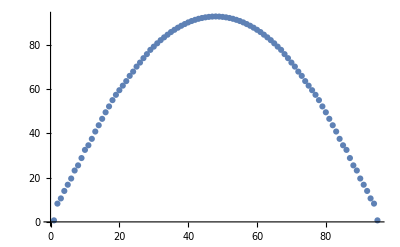

```mathematica
ListPlot[dosGluedSymmNorm]
```

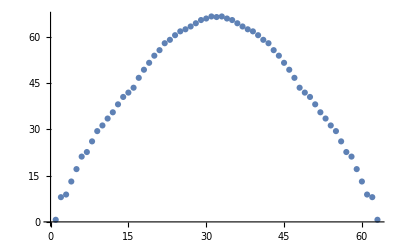

```mathematica
ListPlot[dosGluedSymmNorm]
```

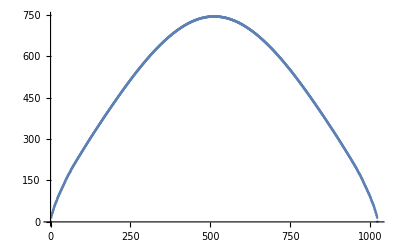

```mathematica
ListPlot[dosGluedSymmNorm]
```

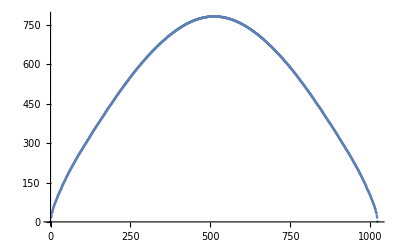

```mathematica
ListPlot[dosGluedSymmNorm]
```

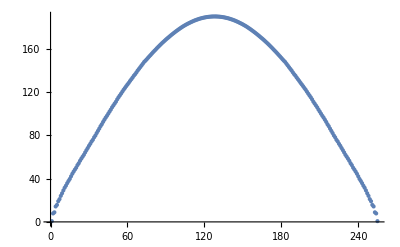

```mathematica
ListPlot[dosGluedSymmNorm]
```

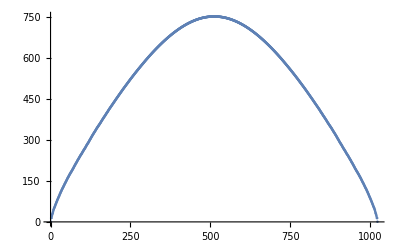

```mathematica
ListPlot[dosGluedSymmNorm]
```

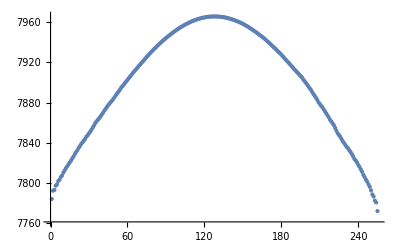

```mathematica
ListPlot[dosGlued]
```

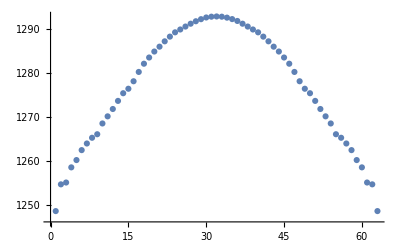

```mathematica
ListPlot[dosGlued]
```

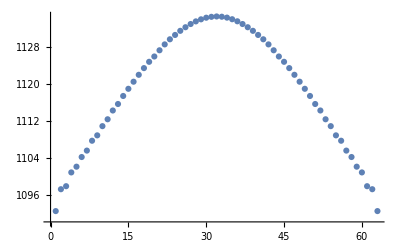

```mathematica
ListPlot[dosGlued]
```

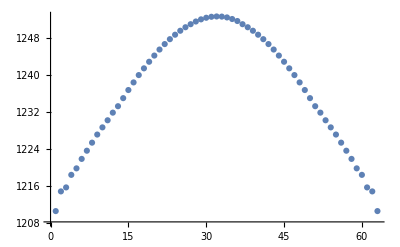

```mathematica
ListPlot[dosGlued]
```

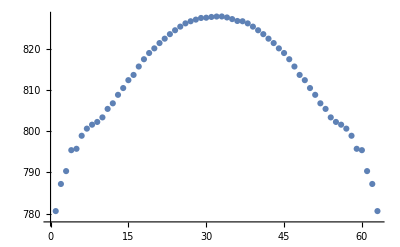

```mathematica
ListPlot[dosGlued]
```

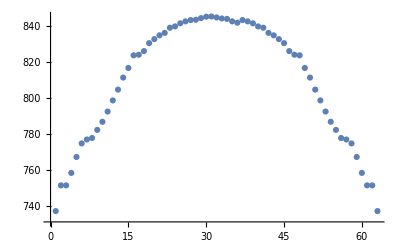

```mathematica
ListPlot[dosGlued]
```

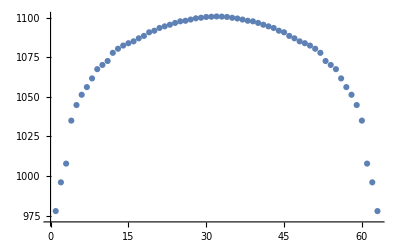

```mathematica
ListPlot[dosGlued]
```

```mathematica
dosGlued=readJuliaVar[fNameWL,"dosArrGlued"];
```

```mathematica
dosGlued//Dimensions
```

{95}

```mathematica
dosGlued//Dimensions
```

{2}

```mathematica
dosGlued
```

```mathematica
dosGlued//MatrixForm
```

(403.059 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.849459 | 418.255 | -0.849459 | -0.849459 | -0.849459 | -0.849459 | -0.849459 | -0.849459 | -0.849459 | -0.849459 | -0.849459 | -0.849459 | -0.849459 | -0.849459 | -0.849459 | 0.254707 | -0.849459
-0.849459 | -0.849459 | 418.567 | 398.39 | -0.849459 | -0.849459 | -0.849459 | -0.849459 | -0.849459 | -0.849459 | -0.849459 | -0.849459 | -0.849459 | -0.849459 | 0.629707 | -0.849459 | -0.849459
11.1377 | 11.1377 | 319.346 | 319.7 | 317.429 | 71.7627 | 11.1377 | 11.1377 | 316.45 | 11.1377 | 11.1377 | 78.2002 | 319.221 | 321.138 | 320.846 | 11.1377 | 11.1377
80.0929 | 80.0929 | 80.0929 | 240.687 | 240.926 | 240.676 | 239.791 | 238.843 | 98.0096 | 239.093 | 239.666 | 240.301 | 240.655 | 240.551 | 80.0929 | 80.0929 | 80.0929
80.0929 | 80.0929 | 80.0929 | 240.135 | 241.718 | 242.228 | 242.072 | 241.77 | 241.645 | 241.697 | 241.593 | 241.749 | 241.374 | 240.176 | 80.0929 | 80.0929 | 80.0929
86.8975 | 86.8975 | 86.8975 | 86.8975 | 237.95 | 238.929 | 238.929 | 239.127 | 239.127 | 239.189 | 238.981 | 239.064 | 238.22 | 86.8975 | 86.8975 | 86.8975 | 86.8975
106.234 | 106.234 | 106.234 | 106.234 | 219.343 | 221.359 | 222.359 | 222.676 | 222.848 | 222.744 | 222.655 | 221.504 | 220.119 | 106.234 | 106.234 | 106.234 | 106.234
106.234 | 106.234 | 106.234 | 106.234 | 106.234 | 219.775 | 221.64 | 222.291 | 222.655 | 222.629 | 221.911 | 220.327 | 106.234 | 106.234 | 106.234 | 106.234 | 106.234
80.0929 | 80.0929 | 80.0929 | 240.135 | 241.718 | 242.228 | 242.072 | 241.77 | 241.645 | 241.697 | 241.593 | 241.749 | 241.374 | 240.176 | 80.0929 | 80.0929 | 80.0929
80.0929 | 80.0929 | 80.0929 | 240.687 | 240.926 | 240.676 | 239.791 | 238.843 | 98.0096 | 239.093 | 239.666 | 240.301 | 240.655 | 240.551 | 80.0929 | 80.0929 | 80.0929
11.1377 | 11.1377 | 319.346 | 319.7 | 317.429 | 71.7627 | 11.1377 | 11.1377 | 316.45 | 11.1377 | 11.1377 | 78.2002 | 319.221 | 321.138 | 320.846 | 11.1377 | 11.1377
-0.849459 | -0.849459 | 418.567 | 398.39 | -0.849459 | -0.849459 | -0.849459 | -0.849459 | -0.849459 | -0.849459 | -0.849459 | -0.849459 | -0.849459 | -0.849459 | 0.629707 | -0.849459 | -0.849459
-0.849459 | 418.255 | -0.849459 | -0.849459 | -0.849459 | -0.849459 | -0.849459 | -0.849459 | -0.849459 | -0.849459 | -0.849459 | -0.849459 | -0.849459 | -0.849459 | -0.849459 | 0.254707 | -0.849459
403.059 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

```mathematica
dosGlued⟦1,1⟧
```

24.9431

```mathematica
dosGluedNormed=(dosGlued-dosGlued⟦1,1⟧)Map[If[#1==0,0,1]&,dosGlued,{-1}];
```

```mathematica
Position[dosGluedNormed,Min[dosGluedNormed]]
```

{{8,17}}

```mathematica
dosGluedNormed⟦8,17⟧
```

-24.25

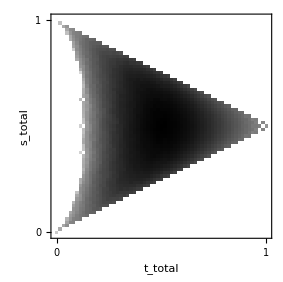

```mathematica
ArrayPlot[dosGluedᵀ,Frame->True,FrameLabel->{"s_total","t_total"},DataRange->{{0,1},{0,1}},FrameTicks->{{Automatic,None},{Automatic,None}},ImageSize->10cm,pltOptMatPlot]
```

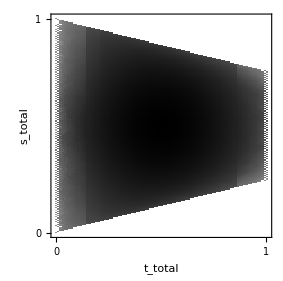

```mathematica
ArrayPlot[dosGluedᵀ,Frame->True,FrameLabel->{"s_total","t_total"},DataRange->{{0,1},{0,1}},FrameTicks->{{Automatic,None},{Automatic,None}},ImageSize->10cm,pltOptMatPlot]
```

```mathematica
Exp[-Infinity]
```

0

```mathematica
ListPlot3D[Map[If[#==0||#<dosGlued⟦1,1⟧,0,#-dosGlued⟦1,1⟧]&,dosGlued,{-1}],PlotRange->All,ColorFunction->"ThermometerColors",AxesLabel->{"s_total","l_total","log g(s,l)"},PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
divNum
```

128

```mathematica
sLst2d=
```

```mathematica
ListPlot3D[Map[If[#==0||#<dosGlued⟦1,1⟧,0,#-dosGlued⟦1,1⟧]&,dosGlued,{-1}],PlotRange->All,ColorFunction->"ThermometerColors",AxesLabel->{"s_total","l_total","log g(s,l)"},PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
ListPlot3D[dosGlued,PlotRange->All,ColorFunction->"ThermometerColors"]
```

-Graphics3D-

```mathematica
ListPlot3D[dosGluedNormed,PlotRange->All,ColorFunction->"ThermometerColors"]
```

-Graphics3D-

```mathematica
dosGluedNormed//Dimensions
```

{255,257}

```mathematica
dosGluedNormed⟦-1,129⟧
```

84.5758

```mathematica
ListPlot3D[Map[If[#<=0,0,#]&,dosGluedNormed,{-1}],PlotRange->All,ColorFunction->"ThermometerColors",AxesLabel->{"sum(s)","sum(l)/2","g(l,s)"}]
```

-Graphics3D-

```mathematica
ListPlot3D[dosGluedNormed,PlotRange->All,ColorFunction->"ThermometerColors"]
```

-Graphics3D-

```mathematica
ListPlot3D[dosGlued,PlotRange->All,ColorFunction->"ThermometerColors"]
```

-Graphics3D-

```mathematica
ListPlot3D[dosGlued,PlotRange->All,ColorFunction->"ThermometerColors"]
```

-Graphics3D-

```mathematica
ListPlot3D[dosGlued,PlotRange->All,ColorFunction->"ThermometerColors"]
```

-Graphics3D-

```mathematica
ListPlot3D[dosGlued,PlotRange->All,ColorFunction->"ThermometerColors"]
```

-Graphics3D-

```mathematica
ListPlot3D[dosGlued,PlotRange->All,ColorFunction->"ThermometerColors"]
```

-Graphics3D-

```mathematica
ListPlot3D[dosGluedNormed,PlotRange->All,ColorFunction->"ThermometerColors"]
```

-Graphics3D-

```mathematica
dosGluedSymm=dosGlued;
```

```mathematica
Do[dosGluedSymm⟦id⟧=dosGlued⟦Length[dosGlued]-id+1⟧,{id,37,Length[dosGlued]}];
```

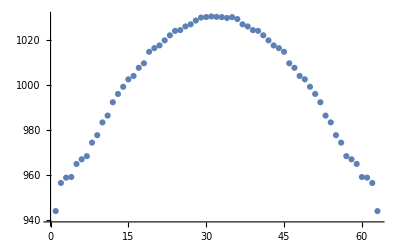

```mathematica
ListPlot[dosGluedSymm]
```

```mathematica
dosGlued
```

{811.453,815.469,815.594,819.161,820.974,822.599,825.448,826.865,828.451,830.372,832.313,833.977,835.719,837.242,838.5,840.453,842.385,843.682,845.292,846.786,848.523,849.633,850.688,851.354,852.281,853.82,854.773,855.068,NaN`,NaN`,NaN`,NaN`,NaN`,NaN`,NaN`,NaN`,854.773,853.82,852.281,851.354,850.688,849.633,848.523,846.786,845.292,843.682,842.385,840.453,838.5,837.242,835.719,833.977,832.313,830.372,828.451,826.865,825.448,822.599,820.974,819.161,815.594,815.469,811.453}

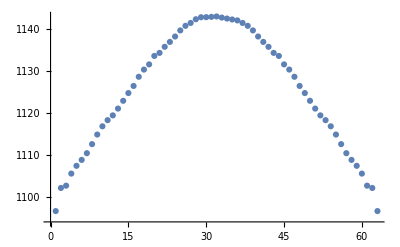

```mathematica
ListPlot[dosGlued,PlotRange->All]
```

```mathematica
dosGluedNormed=dosGlued-dosGlued⟦1⟧+Log[2];
```

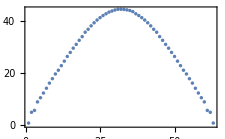

```mathematica
ListPlot[{,dosGluedNormed}ᵀ,pltOptLstNoStyle,ImageSize->8cm]
```

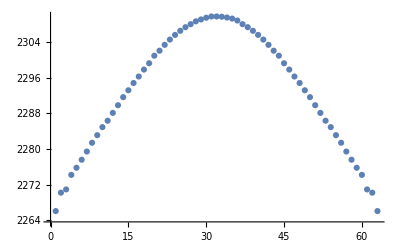

```mathematica
ListPlot[dosGlued]
```

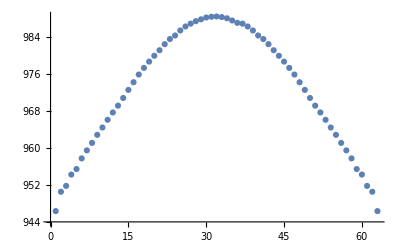

```mathematica
ListPlot[dosGlued]
```

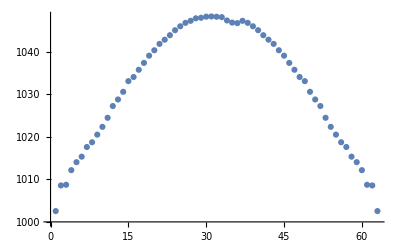

```mathematica
ListPlot[dosGlued]
```

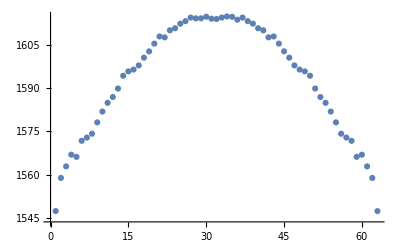

```mathematica
ListPlot[dosGlued]
```

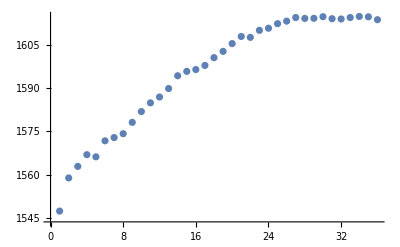

```mathematica
ListPlot[dosGlued⟦1;;36⟧]
```

```mathematica
fNameWL="loops_WL_staggered_divNum_4.0_itNum_409600.0_histDivNum_16.0_cAreaInit_3.0_dosIncrInit_2.0.jld2";
```

```mathematica
itSampleLst=readJuliaVar[fNameWL,"itSampleLst"];
```

```mathematica
itSampleLst
```

{1000,9000,15000,24000}

```mathematica
itSampleLst
```

{1000,10000,33000,66000,80000,111000,134000}

```mathematica
itSampleLst
```

{17000,36000,92000,150000,209000,255000,320000}

```mathematica
histArrSampleLst=readJuliaVar[fNameWL,"histArrSample"];
dosArrSampleLst=readJuliaVar[fNameWL,"dosArrSample"];
```

```mathematica
dosArrSampleLst//Dimensions
```

{10,95}

```mathematica
histArrSampleLst//Dimensions
```

{7,63}

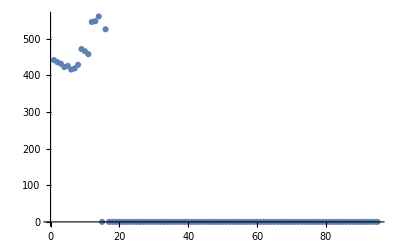

```mathematica
ListPlot[histArrSampleLst⟦3⟧,PlotRange->All]
```

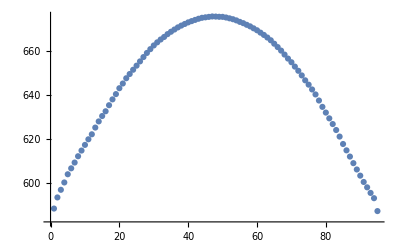

```mathematica
ListPlot[dosArrSampleLst⟦10⟧,PlotRange->All]
```

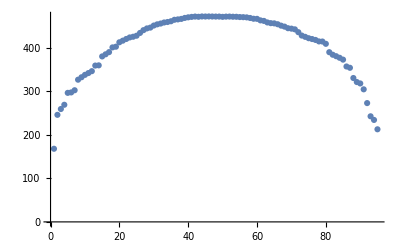

```mathematica
ListPlot[dosArrSampleLst⟦4⟧,PlotRange->All]
```

```mathematica
ListPlot3D[histArrSampleLst⟦4⟧,PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Map[If[#==0,0,#-dosArrSampleLst⟦4,1,1⟧]&,dosArrSampleLst⟦4⟧,{-1}],PlotRange->All,ColorFunction->"ThermometerColors"]
```

-Graphics3D-

```mathematica
dosArrSampleLst⟦4,1,1⟧
```

105.875

```mathematica
Min[dosArrSampleLst⟦7⟧]
```

0.

```mathematica
Map[If[#1==0,0,1]&,dosArrSampleLst⟦7⟧,{-1}]
```

{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,1,1,1,0,0,0,1,0,0,0,1,1,1,0,0},{0,0,0,1,1,1,1,1,0,1,1,1,1,1,0,0,0},{0,0,0,1,1,1,1,1,1,1,1,1,1,1,0,0,0},{0,0,0,0,1,1,1,1,1,1,1,1,1,0,0,0,0},{0,0,0,0,1,1,1,1,1,1,1,1,1,0,0,0,0},{0,0,0,0,0,1,1,1,1,1,1,1,0,0,0,0,0},{0,0,0,0,0,1,1,1,1,1,1,1,0,0,0,0,0},{0,0,0,0,0,0,1,1,1,1,1,0,0,0,0,0,0},{0,0,0,0,0,0,1,1,1,1,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0}}

```mathematica
dosArrNormed4=(dosArrSampleLst⟦7⟧-dosArrSampleLst⟦7,1,1⟧)Map[If[#1==0,0,1]&,dosArrSampleLst⟦7⟧,{-1}];
```

```mathematica
dosArrNormed=(dosArrSampleLst⟦7⟧-dosArrSampleLst⟦7,1,1⟧)Map[If[#1==0,0,1]&,dosArrSampleLst⟦7⟧,{-1}];
```

```mathematica
dosArrNormed4ᵀ⟦5,9⟧
```

0.

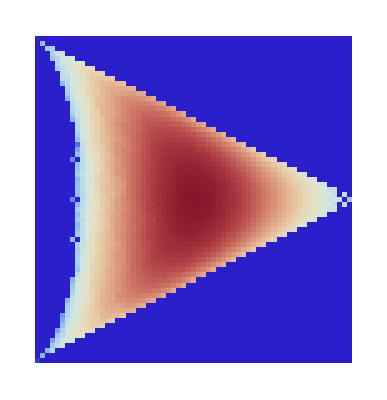

```mathematica
ArrayPlot[dosGluedᵀ,FrameTicks->Automatic,ColorFunction->"ThermometerColors"]
```

```mathematica
dosGluedᵀ⟦48,8⟧
```

0.

```mathematica
ArrayPlot[Map[If[#>0,1,0]&,dosGluedᵀ,{2}],FrameTicks->Automatic]
```

-Graphics-

```mathematica
ArrayPlot[Map[If[#>0,1,0]&,dosGluedᵀ,{2}],FrameTicks->Automatic]
```

-Graphics-

```mathematica
ArrayPlot[Map[If[#>0,1,0]&,dosGluedᵀ,{2}],FrameTicks->Automatic]
```

-Graphics-

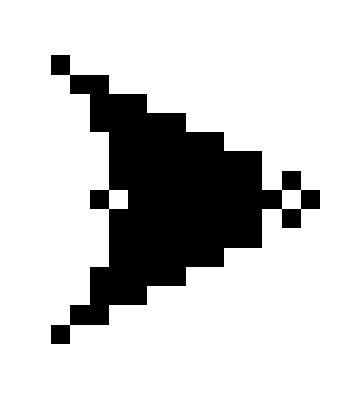

```mathematica
ArrayPlot[Map[If[#>0,1,0]&,dosArrNormed4ᵀ,{2}],FrameTicks->Automatic]
```

```mathematica
ArrayPlot[Map[If[#>0,1,0]&,dosArrNormedᵀ,{2}],FrameTicks->Automatic]
```

-Graphics-

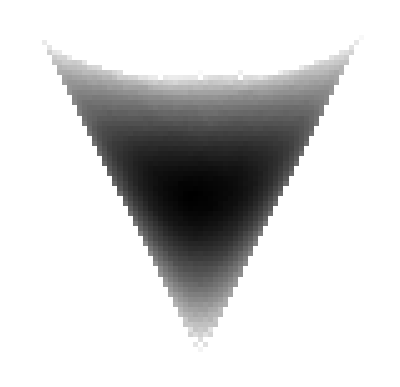

```mathematica
ArrayPlot[dosArrNormed]
```

```mathematica
dosArrNormedᵀ//MatrixForm
```

(0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 2.5625 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 3.10938 | 4.01563 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 4.20313 | 5.14063 | 4.76563 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 2.96875 | 5.46875 | 6.25 | 5.89063 | 5.15625 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 5.25 | 6.29688 | 7.09375 | 7.03125 | 5.54688 | 4.46875 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 4.65625 | 6.32813 | 7.09375 | 7.78125 | 7.23438 | 6.26563 | 4.09375 | 3.6875 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 3.82813 | 6.14063 | 6.89063 | 8.03125 | 7.70313 | 7.09375 | 6.01563 | 4.51563 | 0. | 2.53125 | 0.
0. | 0. | 0. | 1.32813 | 0. | 6.20313 | 6.76563 | 8.04688 | 7.70313 | 7.34375 | 6.17188 | 4.625 | 3.79688 | 0. | 0.375
0. | 0. | 0. | 0. | 3.82813 | 6.01563 | 6.96875 | 7.90625 | 7.64063 | 6.79688 | 5.75 | 4.73438 | 0. | 2.59375 | 0.
0. | 0. | 0. | 0. | 4.23438 | 5.89063 | 7.01563 | 7.59375 | 6.95313 | 6.28125 | 4.375 | 3.92188 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 4.84375 | 6.04688 | 7.03125 | 6.65625 | 5.79688 | 4.51563 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 3.0625 | 4.96875 | 6.04688 | 5.98438 | 4.92188 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 4.03125 | 4.79688 | 4.92188 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 3.07813 | 3.64063 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1.89063 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-1.07813 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

```mathematica
dosArrNormed//Dimensions
```

{63,65}

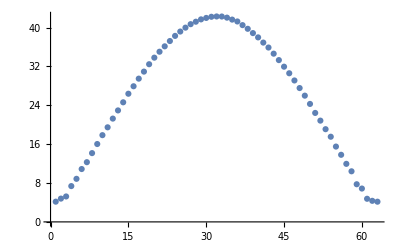

```mathematica
ListPlot[Log[Total[Exp[dosArrNormed],{2}]]]
```

```mathematica
ListPlot3D[dosArrNormed,PlotRange->All,ColorFunction->"ThermometerColors"]
```

-Graphics3D-

```mathematica
ListPlot3D[dosArrNormed,PlotRange->All,ColorFunction->"ThermometerColors"]
```

-Graphics3D-

```mathematica
ListPlot3D[dosArrNormed,PlotRange->All,ColorFunction->"ThermometerColors"]
```

-Graphics3D-

```mathematica
ListPlot3D[dosArrNormed,PlotRange->All,ColorFunction->"ThermometerColors"]
```

-Graphics3D-

```mathematica
ListPlot3D[dosArrSampleLst⟦7⟧,PlotRange->All,ColorFunction->"ThermometerColors"]
```

-Graphics3D-

```mathematica
ListPlot3D[dosArrSampleLst⟦1⟧,PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[dosArrSampleLst⟦2⟧-dosArrSampleLst⟦1⟧,PlotRange->All]
```

-Graphics3D-

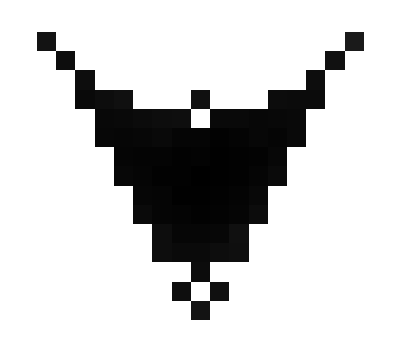

```mathematica
ArrayPlot[dosArrSampleLst⟦4⟧]
```

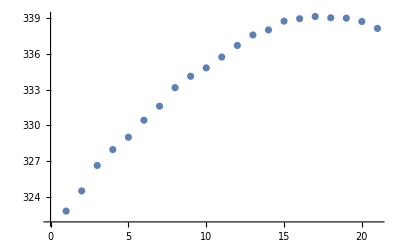

```mathematica
ListPlot[dosArrSampleLst⟦7⟧]
```

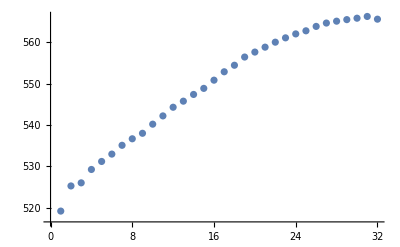

```mathematica
ListPlot[dosArrSampleLst⟦7⟧]
```

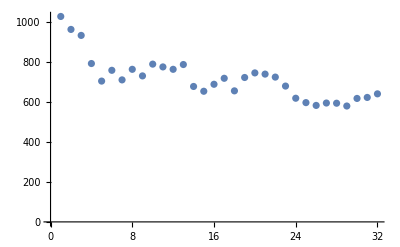

```mathematica
ListPlot[histArrSampleLst⟦7⟧,PlotRange->{Automatic,{0,Automatic}}]
```

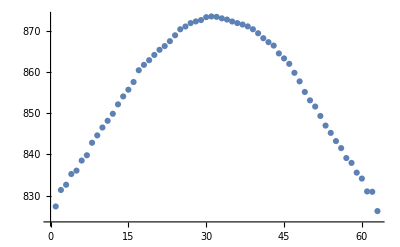

```mathematica
ListPlot[dosArrSampleLst⟦7⟧]
```

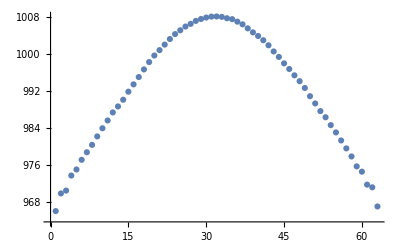

```mathematica
ListPlot[dosArrSampleLst⟦80⟧]
```

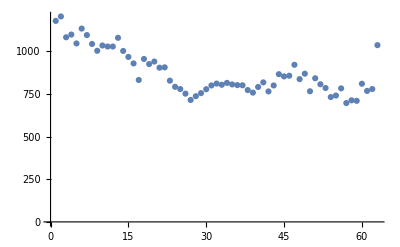

```mathematica
ListPlot[histArrSampleLst⟦7⟧,PlotRange->{Automatic,{0,Automatic}}]
```

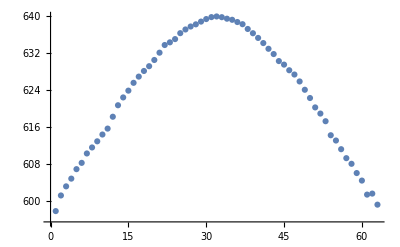

```mathematica
ListPlot[dosArrSampleLst⟦7⟧]
```

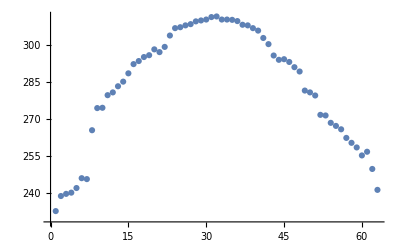

```mathematica
ListPlot[dosArrSampleLst⟦4⟧]
```

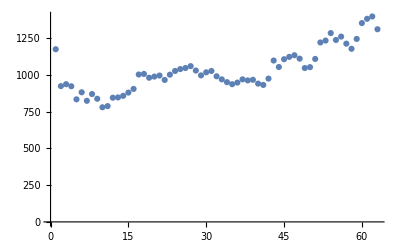

```mathematica
ListPlot[histArrSampleLst⟦7⟧,PlotRange->{Automatic,{0,Automatic}}]
```

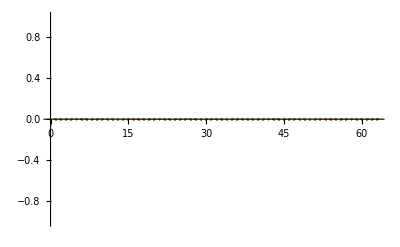

```mathematica
ListPlot[histArrSampleLst]
```

```mathematica
fNameWLSingle="loops_WL.jld2";
```

```mathematica
histArrFlat=readJuliaVarDimRev[fNameWL,"histArr"];
dosArrFlat=readJuliaVarDimRev[fNameWL,"dosArr"];
```

```mathematica
histArr=readJuliaVarDimRev[fNameWL,"histArr"];
dosArr=readJuliaVarDimRev[fNameWL,"dosArr"];
```

```mathematica
dosArr⟦-1⟧
```

200.

```mathematica
Total[dosArr]
```

13492.8

```mathematica
Total[dosArr]
```

36599.3

```mathematica
histArr
```

{2710,3015,2787,3035,2995,3108,3181,3244,3147,3033,2936,2962,2919,2815,2898,2912,2861,2754,2866,2755,2844,2722,2702,2742,2735,2837,2847,2728,2468,2484,2399,2465,2384,2362,2292,2266,1833,1818,1747,1592,1526,1464,1479,1377,1334,1386,1305,1313,1171,1178,1177,1150,1090,1158,1067,1052,1041,924,907,899,913,977,1014,1011,993,939,933,922,881,869,878,835,846,835,867,921,881,916,909,905,938,947,995,1006,1012,1044,1042,1054,1021,1074,1071,1012,988,987,966,964,986,996,1033,1049,1043,1017,1010,1006,1003,984,969,988,975,969,953,910,903,917,901,878,891,863,874,892,873,931,919,957,941,999,1015,1012,956,963,965,978,970,1000,1015,1015,1022,1015,975,940,960,970,973,931,958,957,927,969,1029,1031,1016,1015,1014,1017,1001,1016,1051,1095,1080,1124,1154,1168,1175,1151,1164,1212,1271,1265,1261,1328,1286,1318,1319,1318,1338,1385,1355,1439,1472,1532,1572,1542,1520,1516,1531,1559,1525,1533,1537,1565,1568,1531,1543,1579,1550,1533,1488,1475,1460,1436,1383,1475,1440,1416,1464,1501,1561,1760,1752,1818,1787,1841,1789,1899,1915,1953,2047,2222,2328,2537,2593,2546,2681,2812,2903,3139,3087,3216,3145,3258,3305,3223,3218,3139,3205,3166,3142,3145,3005,3009,3024,3005,2951,3061,2949,3008,3002,2983,3057,3017,3067,3129,2982,2997,3301}

```mathematica
dosArrFlatSymm=(dosArrFlat+Reverse[dosArrFlat])/2;
```

```mathematica
dosArrSymm=(dosArr+Reverse[dosArr])/2
```

{1096.6,1102.89,1104.02,1110.16,1110.05,1114.68,1116.72,1119.96,1122.12,1124.2,1126.87,1129.2,1130.17,1132.58,1134.84,1136.54,1139.91,1141.63,1144.48,1145.98,1148.02,1149.62,1151.53,1153.71,1155.92,1158.1,1159.66,1161.97,1163.57,1165.9,1167.36,1169.62,1171.15,1172.89,1175.01,1176.87,1178.63,1180.09,1182.13,1183.57,1185.32,1187.52,1189.06,1190.45,1192.29,1194.59,1196.13,1197.91,1199.55,1200.98,1202.62,1204.42,1205.86,1207.91,1209.14,1211.03,1212.73,1214.13,1215.48,1217.19,1218.73,1220.92,1222.77,1224.28,1226.1,1227.44,1228.95,1230.32,1231.63,1233.44,1235.01,1236.57,1238.61,1240.21,1241.73,1243.4,1244.66,1245.71,1247.31,1248.8,1249.98,1251.09,1252.55,1254.02,1255.28,1256.69,1257.77,1259.2,1260.3,1261.55,1262.37,1263.41,1264.71,1265.6,1266.52,1267.55,1268.44,1269.3,1270.36,1271.48,1272.28,1272.78,1273.53,1274.54,1275.21,1275.96,1276.44,1277.13,1277.67,1278.28,1278.99,1279.09,1279.59,1280.09,1280.29,1280.78,1281.16,1281.73,1282.34,1282.54,1282.64,1283.13,1283.1,1283.49,1283.81,1284.03,1284.13,1284.19,1284.13,1284.03,1283.81,1283.49,1283.1,1283.13,1282.64,1282.54,1282.34,1281.73,1281.16,1280.78,1280.29,1280.09,1279.59,1279.09,1278.99,1278.28,1277.67,1277.13,1276.44,1275.96,1275.21,1274.54,1273.53,1272.78,1272.28,1271.48,1270.36,1269.3,1268.44,1267.55,1266.52,1265.6,1264.71,1263.41,1262.37,1261.55,1260.3,1259.2,1257.77,1256.69,1255.28,1254.02,1252.55,1251.09,1249.98,1248.8,1247.31,1245.71,1244.66,1243.4,1241.73,1240.21,1238.61,1236.57,1235.01,1233.44,1231.63,1230.32,1228.95,1227.44,1226.1,1224.28,1222.77,1220.92,1218.73,1217.19,1215.48,1214.13,1212.73,1211.03,1209.14,1207.91,1205.86,1204.42,1202.62,1200.98,1199.55,1197.91,1196.13,1194.59,1192.29,1190.45,1189.06,1187.52,1185.32,1183.57,1182.13,1180.09,1178.63,1176.87,1175.01,1172.89,1171.15,1169.62,1167.36,1165.9,1163.57,1161.97,1159.66,1158.1,1155.92,1153.71,1151.53,1149.62,1148.02,1145.98,1144.48,1141.63,1139.91,1136.54,1134.84,1132.58,1130.17,1129.2,1126.87,1124.2,1122.12,1119.96,1116.72,1114.68,1110.05,1110.16,1104.02,1102.89,1096.6}

```mathematica
dosArr
```

{550.,570.188,561.188,573.625,575.625,581.5,587.438,590.5,593.75,595.688,598.375,603.875,607.688,609.25,611.5,613.438,619.625,626.,629.375,631.563,633.125,638.438,640.875,640.563,645.938,647.375,650.313,652.75,653.938,657.375,659.563,660.063,661.25,664.313,665.625,666.75,669.125,671.25,674.063,674.813,676.875,678.875,680.688,684.813,688.,690.625,695.188,697.563,699.813,701.313,703.875,705.063,708.,710.625,711.938,713.625,715.938,719.438,720.5,723.,723.875,725.75,726.75,727.875,731.375,733.75,735.75,736.625,738.688,739.75,741.438,742.625,744.438,745.375,747.75,748.625,749.5,750.438,751.438,753.938,755.5,759.125,760.063,761.75,762.625,763.375,764.375,766.313,767.563,768.875,770.875,771.625,773.,773.438,774.188,774.875,776.438,778.5,778.625,779.625,780.625,781.938,782.875,784.,784.938,784.75,785.,785.313,785.688,786.375,787.188,787.25,787.875,788.063,788.688,788.438,789.375,789.938,789.688,789.813,790.063,790.438,790.375,790.688,790.188,789.813,790.063,790.25,790.25,790.563,790.563,790.563,790.313,790.063,790.188,789.313,789.563,789.125,788.813,788.688,788.563,788.625,788.563,788.625,788.125,787.813,787.375,786.75,786.313,786.188,785.125,784.375,783.438,782.5,781.625,780.25,778.875,778.75,778.5,778.125,777.188,776.375,775.625,774.563,773.813,771.313,770.125,768.75,767.625,766.438,766.125,763.25,761.125,759.75,757.188,755.5,753.625,753.25,751.125,749.,747.563,745.438,744.25,742.625,741.,739.625,737.5,734.313,732.313,731.563,729.125,724.813,722.938,720.5,719.313,715.875,712.313,710.563,709.25,707.563,706.25,705.313,702.5,701.313,697.313,696.188,691.688,689.75,688.625,687.125,683.5,682.,679.813,677.5,674.875,669.438,666.188,658.938,657.375,653.75,651.813,648.688,646.938,644.5,641.5,638.375,634.938,632.188,631.313,628.,626.375,623.875,623.063,619.188,616.188,613.813,611.,606.375,603.313,602.438,601.75,600.5,597.438,596.25,593.188,588.,581.25,578.375,569.25,560.063,552.375,555.625,547.688,552.,500.688}

```mathematica
dosArr
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,14.,43.,70.,100.,106.,130.,154.,221.,237.,234.,293.,343.,334.,344.,351.,382.,383.,382.,396.,404.,410.,413.,418.,422.,422.,457.,463.,487.,496.,496.,517.,568.,571.,599.,650.,645.,651.,662.,697.,709.,737.,774.,777.,773.,788.,789.,802.,805.,834.,832.,839.,858.,877.,888.,885.,906.,931.,936.,940.,945.,948.,995.,1014.,1021.,1023.,1035.,1037.,1035.,1037.,1041.,1045.,1045.,1052.,1061.,1065.,1068.,1071.,1068.,1073.,1073.,1092.,1095.,1097.,1101.,1106.,1111.,1113.,1116.,1117.,1123.,1136.,1138.,1139.,1138.,1134.,1138.,1140.,1142.,1141.,1149.,1150.,1153.,1155.,1158.,1158.,1156.,1158.,1173.,1170.,1169.,1169.,1168.,1162.,1161.,1162.,1160.,1163.,1162.,1164.,1164.,1164.,1166.,1168.,1169.,1163.,1159.,1152.,1155.,1148.,1148.,1149.,1141.,1144.,1135.,1133.,1127.,1120.,1123.,1121.,1121.,1119.,1117.,1112.,1110.,1110.,1105.,1105.,1097.,1100.,1098.,1098.,1084.,1082.,1080.,1081.,1079.,1073.,1070.,1067.,1057.,1033.,1023.,995.,996.,990.,985.,982.,964.,960.,950.,950.,944.,940.,938.,930.,928.,924.,915.,915.,914.,907.,886.,882.,881.,878.,871.,873.,864.,860.,860.,856.,852.,848.,845.,826.,822.,812.,790.,769.,765.,763.,762.,734.,730.,726.,726.,714.,716.,714.,701.,698.,680.,679.,673.,661.,604.,613.,595.,555.,522.,519.,500.,482.,466.,455.,451.,443.,429.,395.,396.,367.,347.,305.,270.,267.,155.,91.,43.,49.,33.,0.,0.,0.,0.,0.}

```mathematica
dosArr⟦1⟧
```

0.

```mathematica
dosArrNormed=dosArr-Min[dosArr⟦{1,-1}⟧]+Log[2];
```

```mathematica
dosArrFlatSymmNormed=dosArrFlatSymm-Min[dosArrFlatSymm⟦{1,-1}⟧]+Log[2];
```

```mathematica
dosArrSymmNormed=dosArrSymm-Min[dosArrSymm⟦{1,-1}⟧]+Log[2];
```

```mathematica
divNum=32;
```

```mathematica
isingELst={-2 divNum^2}~Join~Range[-2 divNum^2+8,2 divNum^2-8,4]~Join~{2 divNum^2};
```

```mathematica
isingELstFull=Range[-2 divNum^2,2 divNum^2,4];
```

```mathematica
{isingELstNormed,isingELstFullNormed}={isingELst,isingELstFull}/(divNum^2);
```

```mathematica
isingELst
```

{-512,-504,-500,-496,-492,-488,-484,-480,-476,-472,-468,-464,-460,-456,-452,-448,-444,-440,-436,-432,-428,-424,-420,-416,-412,-408,-404,-400,-396,-392,-388,-384,-380,-376,-372,-368,-364,-360,-356,-352,-348,-344,-340,-336,-332,-328,-324,-320,-316,-312,-308,-304,-300,-296,-292,-288,-284,-280,-276,-272,-268,-264,-260,-256,-252,-248,-244,-240,-236,-232,-228,-224,-220,-216,-212,-208,-204,-200,-196,-192,-188,-184,-180,-176,-172,-168,-164,-160,-156,-152,-148,-144,-140,-136,-132,-128,-124,-120,-116,-112,-108,-104,-100,-96,-92,-88,-84,-80,-76,-72,-68,-64,-60,-56,-52,-48,-44,-40,-36,-32,-28,-24,-20,-16,-12,-8,-4,0,4,8,12,16,20,24,28,32,36,40,44,48,52,56,60,64,68,72,76,80,84,88,92,96,100,104,108,112,116,120,124,128,132,136,140,144,148,152,156,160,164,168,172,176,180,184,188,192,196,200,204,208,212,216,220,224,228,232,236,240,244,248,252,256,260,264,268,272,276,280,284,288,292,296,300,304,308,312,316,320,324,328,332,336,340,344,348,352,356,360,364,368,372,376,380,384,388,392,396,400,404,408,412,416,420,424,428,432,436,440,444,448,452,456,460,464,468,472,476,480,484,488,492,496,500,504,512}

```mathematica
isingELst=Delete[isingELst,2];
isingELst=Delete[isingELst,-2];
```

Delete::partw: Part {-2} of Delete[{-32,-24,-20,-16,-12,-8,-4,0,4,8,«6»}] does not exist.

```mathematica
divNum^2
```

1024

```mathematica
dosArr⟦1⟧
```

76.25

```mathematica
dosArrNormed⟦1⟧
```

0.693147

```mathematica
xyLabsWL=matexLstFunc[{"E/2L^2","\\log g \\left( E \\right)"},labMag];
```

```mathematica
xyLabsWL
```

{-Graphics-,-Graphics-}

```mathematica
legLstWLExact=matexLstFunc[{"\\mathrm{Wang\\, Landau}","\\mathrm{exact}"},labMag];
```

```mathematica
titleWL8=MaTeX["8 \\times 8",Magnification->labMag];
```

```mathematica
titleWL16=MaTeX["16 \\times 16 \\, , \\, 3.2 \\times 10^6 \\mathrm{\\, iterations}",Magnification->labMag];
```

```mathematica
dosGluedNormed//Dimensions
```

{63}

```mathematica
isingELstNormed//Dimensions
```

{63}

```mathematica
,{isingELstFullNormed,gExactLst16}ᵀ
```

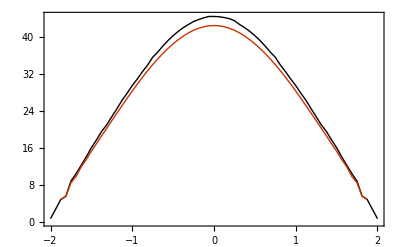

```mathematica
ListLinePlot[{{isingELstNormed,dosGluedNormed}ᵀ,{isingELstFullNormed,gExactLst8}ᵀ},pltOptLstNoStyle,PlotStyle->lineStyleLstDataThick,Axes->False,FrameLabel->xyLabsWL,PlotLegends->Placed[LineLegend[legLstWLExact,Spacings->0.3],Scaled[{0.5,0.5}]],PlotLabel->titleWL8]
```

```mathematica
gExactLst32=splot⟦All,2⟧;
```

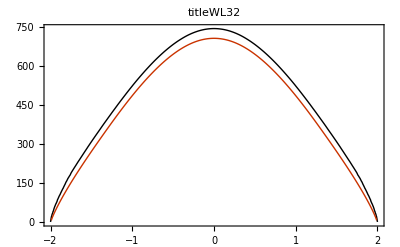

```mathematica
ListLinePlot[{{isingELstNormed,dosGluedSymmNorm}ᵀ,{isingELstFullNormed,gExactLst32}ᵀ},pltOptLstNoStyle,PlotStyle->lineStyleLstDataThick,Axes->False,FrameLabel->xyLabsWL,PlotLegends->Placed[LineLegend[legLstWLExact,Spacings->0.3],Scaled[{0.5,0.5}]],PlotLabel->titleWL32]
```

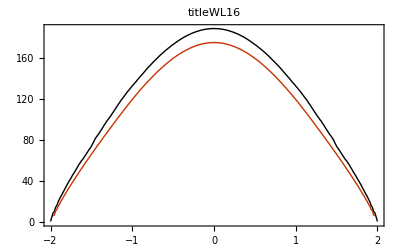

```mathematica
ListLinePlot[{{isingELstNormed,dosGluedSymmNorm}ᵀ,{isingELstFullNormed,gExactLst16}ᵀ},pltOptLstNoStyle,PlotStyle->lineStyleLstDataThick,Axes->False,FrameLabel->xyLabsWL,PlotLegends->Placed[LineLegend[legLstWLExact,Spacings->0.3],Scaled[{0.5,0.5}]],PlotLabel->titleWL16]
```

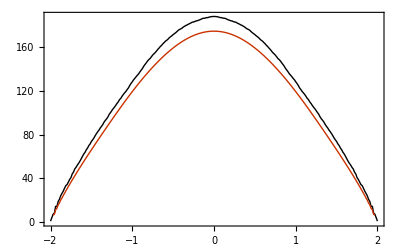

```mathematica
ListLinePlot[{{isingELstNormed,dosArrSymmNormed}ᵀ,{isingELstFullNormed,gExactLst16}ᵀ},pltOptLstNoStyle,PlotStyle->lineStyleLstDataThick,Axes->False,FrameLabel->xyLabsWL,PlotLegends->Placed[LineLegend[legLstWLExact,Spacings->0.3],Scaled[{0.5,0.5}]],PlotLabel->titleWL16]
```

```mathematica
titleFlatExplored=MaTeX["16 \\times 16 \\mathrm{\, flatness\, conditions}",Magnification->labMag]
```

-Graphics-

```mathematica
gExactLst16=splot⟦All,2⟧;
```

```mathematica
gExactLst8=splot⟦All,2⟧;
```

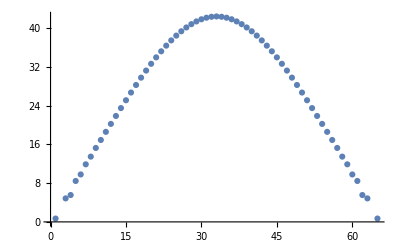

```mathematica
ListPlot[splot⟦All,2⟧]
```

```mathematica
legLstWLFlatExplored=matexLstFunc[{"\\mathrm{explored (good)}","\\mathrm{all (bad)}","\\mathrm{exact}"},labMag];
```

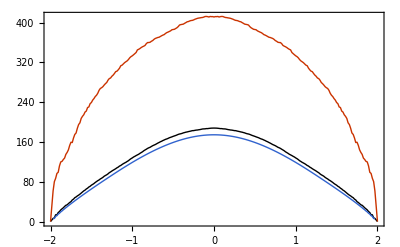

```mathematica
ListLinePlot[{{isingELstNormed,dosArrSymmNormed}ᵀ,{isingELstNormed,dosArrFlatSymmNormed}ᵀ,{isingELstFullNormed,gExactLst16}ᵀ},pltOptLstNoStyle,PlotStyle->lineStyleLstDataThick,Axes->False,FrameLabel->xyLabsWL,PlotLegends->Placed[LineLegend[legLstWLFlatExplored,Spacings->0.3],Scaled[{0.5,0.7}]],PlotLabel->titleFlatExplored]
```

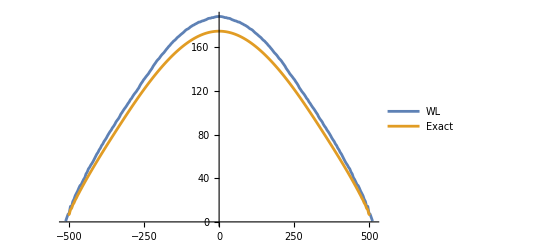

```mathematica
ListLinePlot[{{isingELst,dosArrSymmNormed}ᵀ,{isingELstFull,gExactLst16}ᵀ},PlotLegends->{"WL","Exact"}]
```

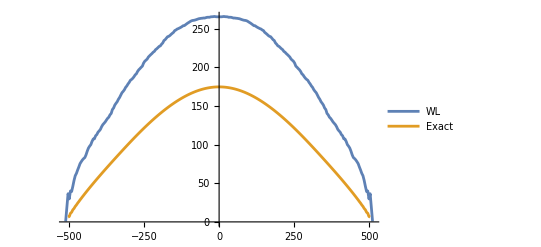

```mathematica
ListLinePlot[{{isingELst,dosArrSymmNormed}ᵀ,{isingELstFull,gExactLst16}ᵀ},PlotLegends->{"WL","Exact"}]
```

```mathematica
ListLinePlot[{{isingELst,dosArrSymmNormed}ᵀ,{isingELstFull,gExactLst16}ᵀ},PlotLegends->{"WL","Exact"}]
```

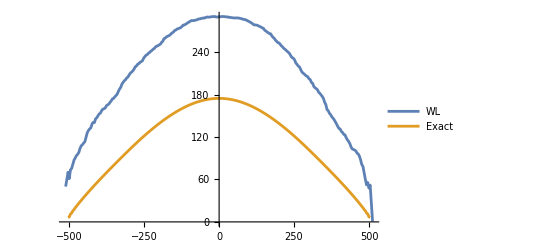

```mathematica
ListLinePlot[{{isingELst,dosArrNormed}ᵀ,{isingELstFull,gExactLst16}ᵀ},PlotLegends->{"WL","Exact"}]
```

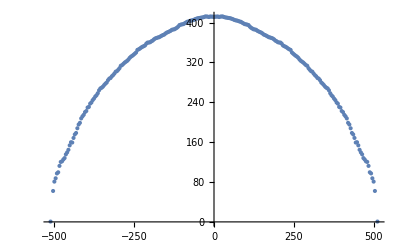

```mathematica
ListPlot[{isingELst,dosArrFlatSymmNormed}ᵀ]
```

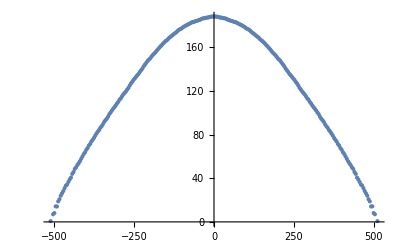

```mathematica
ListPlot[{isingELst,dosArrSymmNormed}ᵀ]
```

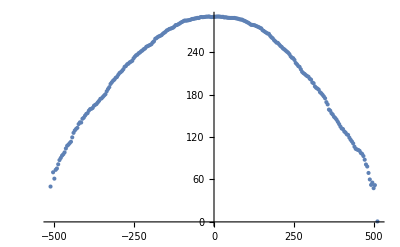

```mathematica
ListPlot[{isingELst,dosArrNormed}ᵀ]
```

```mathematica
ListPlot[{isingELst,dosArrNormed}ᵀ]
```

-Graphics-

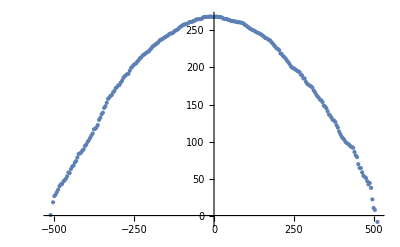

```mathematica
ListPlot[{isingELst,dosArrNormed}ᵀ]
```

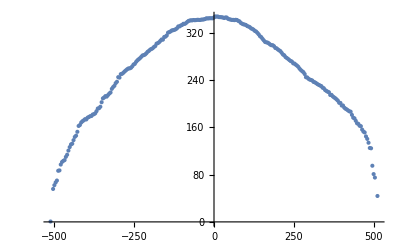

```mathematica
ListPlot[{isingELst,dosArrNormed}ᵀ]
```

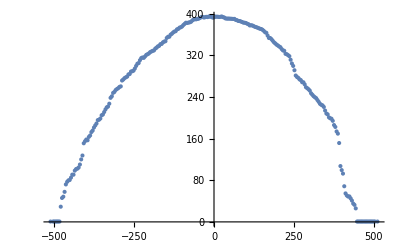

```mathematica
ListPlot[{isingELst,dosArrNormed}ᵀ]
```

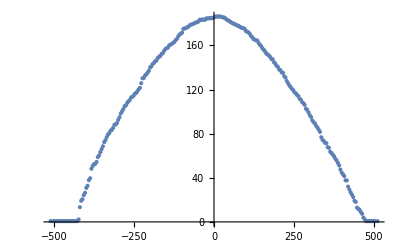

```mathematica
ListPlot[{isingELst,dosArrNormed}ᵀ]
```

```mathematica
ListPlot[{isingELst,dosArrNormed}ᵀ]
```

-Graphics-

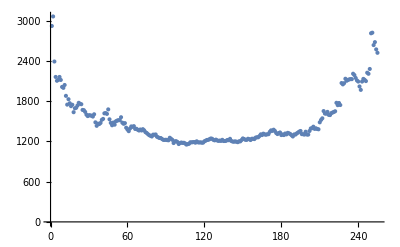

```mathematica
ListPlot[histArr]
```

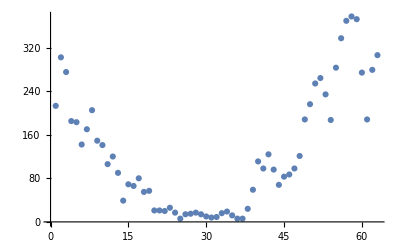

```mathematica
ListPlot[histArr]
```

```mathematica
gExactLst16=gExactLst;
```

```mathematica
gExactLst=splot⟦All,2⟧;
```

```mathematica
gExactLst//Dimensions
```

{37}

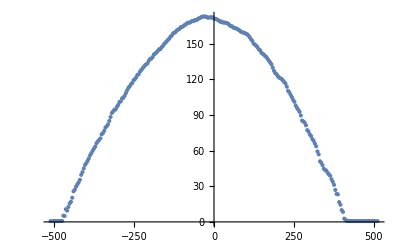

```mathematica
ListPlot[{isingELst,dosArrNormed}ᵀ]
```

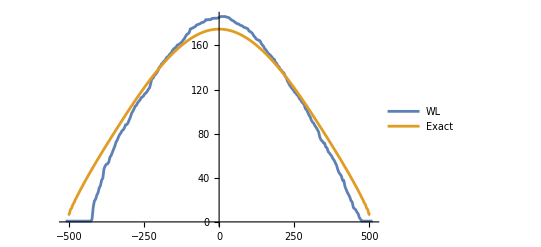

```mathematica
ListLinePlot[{{isingELst,dosArrNormed}ᵀ,{isingELstFull,gExactLst16}ᵀ},PlotLegends->{"WL","Exact"}]
```

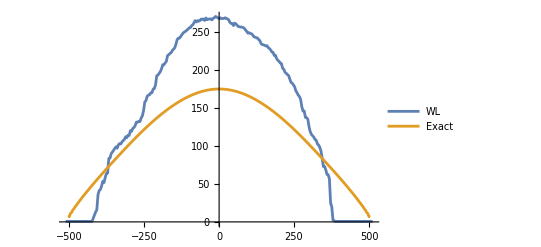

```mathematica
ListLinePlot[{{isingELst,dosArrNormed}ᵀ,{isingELstFull,gExactLst16}ᵀ},PlotLegends->{"WL","Exact"}]
```

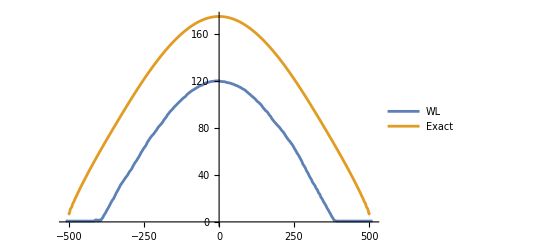

```mathematica
ListLinePlot[{{isingELst,dosArrNormed}ᵀ,{isingELstFull,gExactLst16}ᵀ},PlotLegends->{"WL","Exact"}]
```

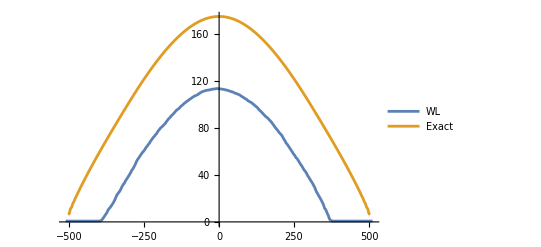

```mathematica
ListLinePlot[{{isingELst,dosArrNormed}ᵀ,{isingELstFull,gExactLst16}ᵀ},PlotLegends->{"WL","Exact"}]
```

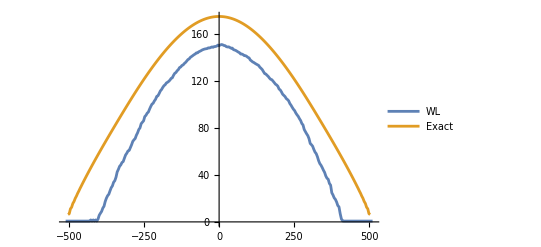

```mathematica
ListLinePlot[{{isingELst,dosArrNormed}ᵀ,{isingELstFull,gExactLst16}ᵀ},PlotLegends->{"WL","Exact"}]
```

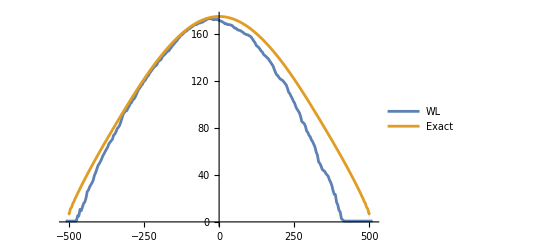

```mathematica
ListLinePlot[{{isingELst,dosArrNormed}ᵀ,{isingELstFull,gExactLst16}ᵀ},PlotLegends->{"WL","Exact"}]
```

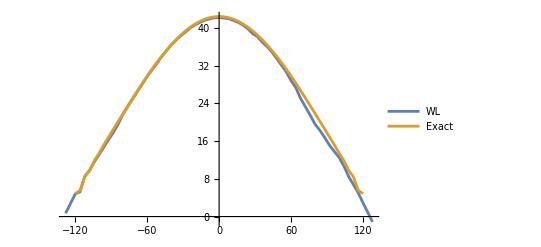

```mathematica
ListLinePlot[{{isingELst,dosArrNormed}ᵀ,{isingELstFull,gExactLst8}ᵀ},PlotLegends->{"WL","Exact"}]
```

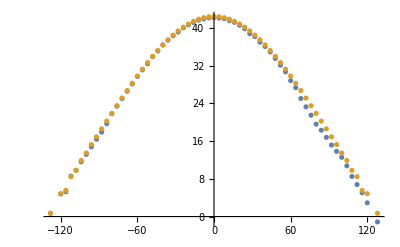

```mathematica
ListPlot[{{isingELst,dosArrNormed}ᵀ,{isingELstFull,gExactLst8}ᵀ}]
```

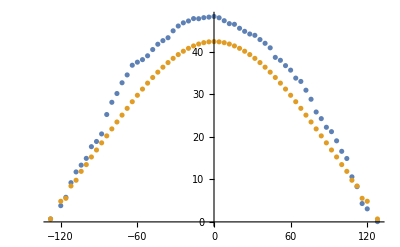

```mathematica
ListPlot[{{isingELst,dosArrNormed}ᵀ,{isingELstFull,gExactLst8}ᵀ}]
```

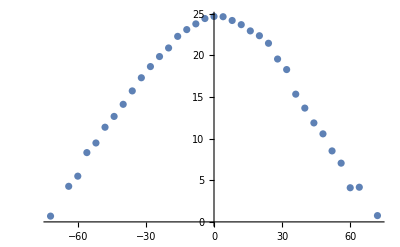

```mathematica
ListPlot[{isingELst,dosArrNormed}ᵀ,]
```

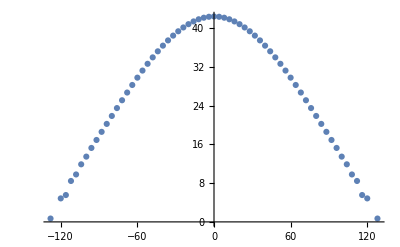

```mathematica
ListPlot[{isingELstFull,gExactLst}ᵀ]
```

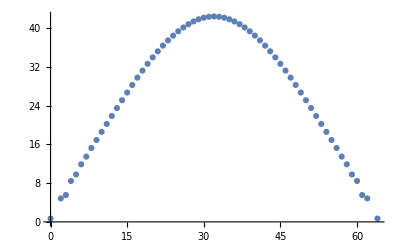

```mathematica
ListPlot[splot]
```

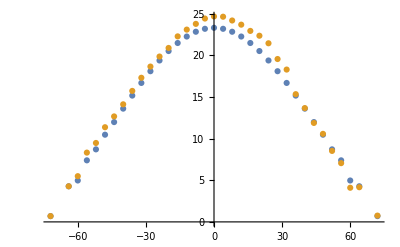

```mathematica
ListPlot[{{isingELstFull,gExactLst}ᵀ,{isingELst,dosArrNormed}ᵀ}]
```

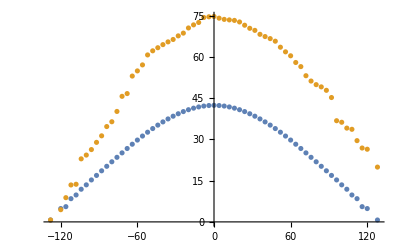

```mathematica
ListPlot[{{isingELstFull,gExactLst}ᵀ,{isingELst,dosArrNormed}ᵀ}]
```

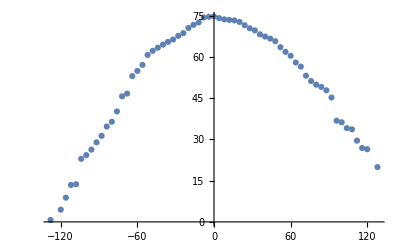

```mathematica
ListPlot[{isingELst,dosArrNormed}ᵀ]
```

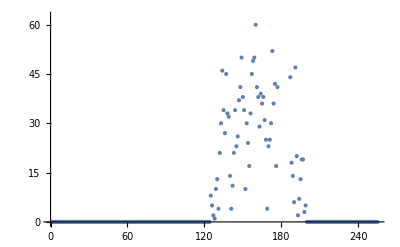

```mathematica
ListPlot[histArr]
```

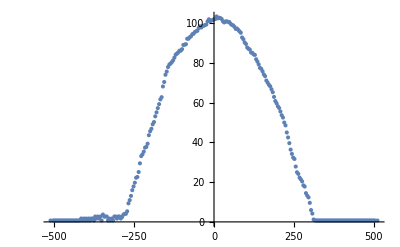

```mathematica
ListPlot[{isingELst,dosArrNormed}ᵀ]
```

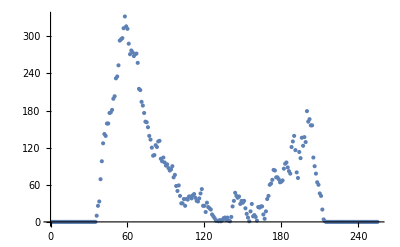

```mathematica
ListPlot[histArr]
```

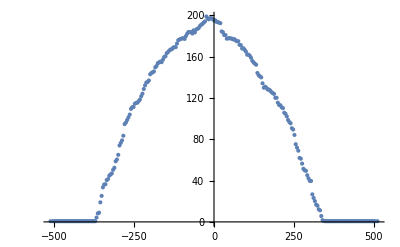

```mathematica
ListPlot[{isingELst,dosArrNormed}ᵀ]
```

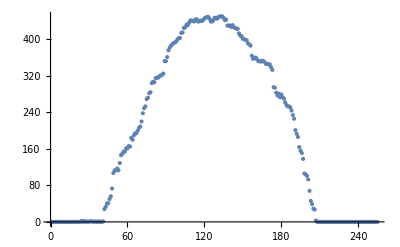

```mathematica
ListPlot[histArr]
```

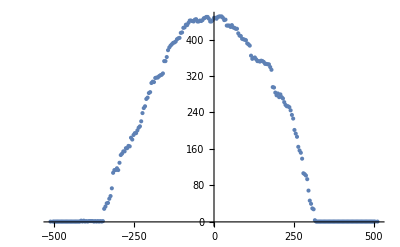

```mathematica
ListPlot[{isingELst,dosArrNormed}ᵀ]
```

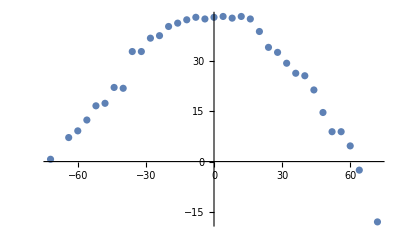

```mathematica
ListPlot[{isingELst,dosArrNormed}ᵀ]
```

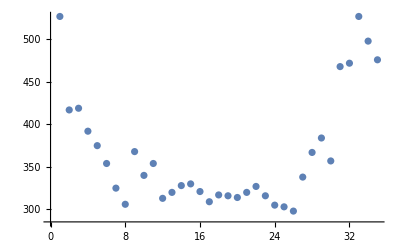

```mathematica
ListPlot[histArr]
```

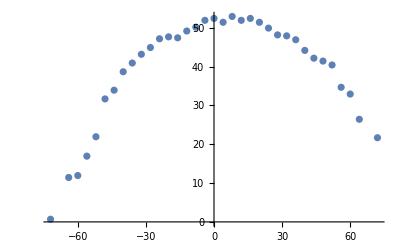

```mathematica
ListPlot[{isingELst,dosArrNormed}ᵀ]
```

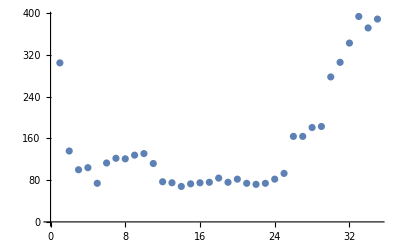

```mathematica
ListPlot[histArr]
```

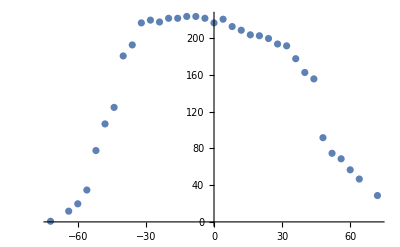

```mathematica
ListPlot[{isingELst,dosArrNormed}ᵀ]
```

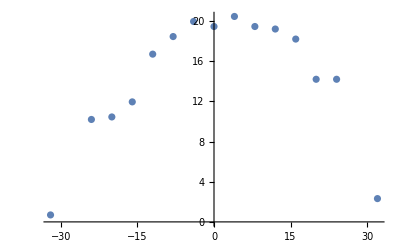

```mathematica
ListPlot[{isingELst,dosArrNormed}ᵀ]
```

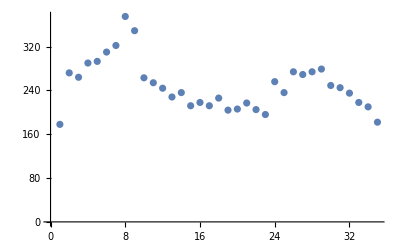

```mathematica
ListPlot[histArr]
```

```mathematica
ListPlot[{isingELst,dosArrNormed}ᵀ]
```

-Graphics-

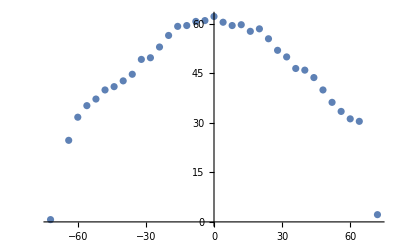

```mathematica
ListPlot[{isingELst,dosArrNormed}ᵀ]
```

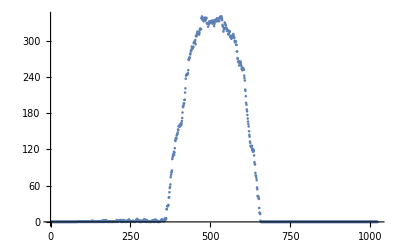

```mathematica
ListPlot[histArr]
```

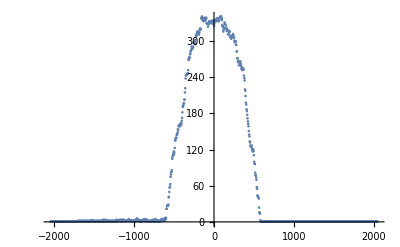

```mathematica
ListPlot[{isingELst,dosArrNormed}ᵀ]
```

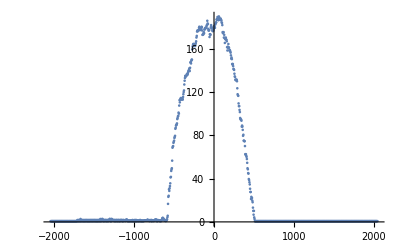

```mathematica
ListPlot[{isingELst,dosArrNormed}ᵀ]
```

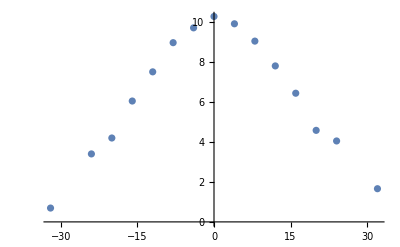

```mathematica
ListPlot[{isingELst,dosArrNormed}ᵀ]
```

```mathematica
Delete[isingELst,-2]
```

{-32,-28,-24,-20,-16,-12,-8,-4,0,4,8,12,16,20,24,32}

```mathematica
dosArr//Dimensions
```

{15}

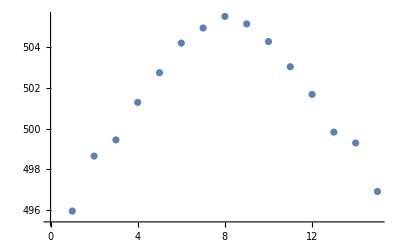

```mathematica
ListPlot[dosArr]
```

```mathematica
histArr=readJuliaVarDimRev[fNameWL,"histArr"];
```

```mathematica
dosArr=readJuliaVarDimRev[fNameWL,"dosArr"];
```

```mathematica
histArrSingle=histArr;
```

```mathematica
fNameSingle="loops_WL_single_divNum_4_itNum_40960000_histDivNum_16_cAreaInit_3_dosIncrInit_2.0.jld2";
```

```mathematica
histArrSingle=readJuliaVarDimRev[fNameSingle,"histArr"];
```

```mathematica
histArrSingle=readJuliaVarDimRev[fNameWLSingle,"histArr"];
```

```mathematica
histArrSingle//Dimensions
```

{80,80}

```mathematica
histDivNum=Length[histArr];
```

```mathematica
histDivNum=Length[histArrSingle];
```

```mathematica
histArr//Dimensions
```

{512,512}

```mathematica
Max[histArrSingle]
```

281

```mathematica
Min[histArrSingle]
```

0

```mathematica
Total[histArrSingle,-1]
```

40960000

```mathematica
Max[{{1,2},{3,4}}]
```

4

```mathematica
Total[histArr,-1]
```

51200

```mathematica
Max[histArr]
```

122

```mathematica
histArr
```

```mathematica
histArrNon0=Map[#>0&,histArrSingle,{2}]/.subBoolIntPlot;
```

```mathematica
histArrNon0//Dimensions
```

{256,256}

```mathematica
256^2
```

65536

```mathematica
Total[histArrNon0,-1]
```

83

```mathematica
Max[histArr]/Total[histArr,-1]//N
```

0.00238281

```mathematica
Max[histArr]/Total[histArr,-1]//N
```

0.00149918

```mathematica
Length[histArrSingle]
```

16

```mathematica
Length[histArrSingle⟦1⟧]
```

16

```mathematica
histArr3d=Table[{ii,jj,histArrSingle⟦ii,jj⟧},{ii,Length[histArrSingle]},{jj,Length[histArrSingle⟦1⟧]}];
```

```mathematica
testArr=histArr⟦2031;;2080,2031;;2080⟧;
```

```mathematica
testArr3d=Table[{ii,jj,testArr⟦ii,jj⟧},{ii,Length[testArr]},{jj,Length[testArr⟦1⟧]}];
```

```mathematica
ListPlot3D[histArr3d]
```

-Graphics3D-

```mathematica
ListPlot3D[testArr]
```

-Graphics3D-

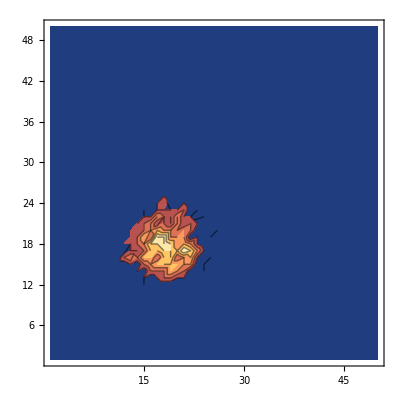

```mathematica
ListContourPlot[testArr]
```

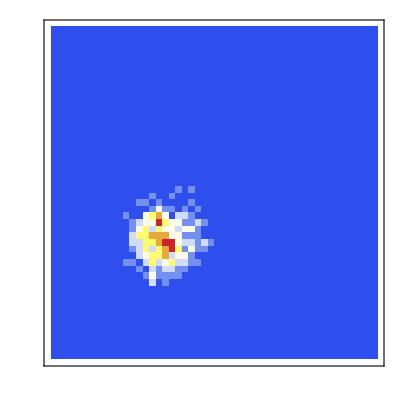

```mathematica
ArrayPlot[Transpose@histArr⟦2031;;2080,2031;;2080⟧,pltOptMatPlot,DataReversed->True,ColorFunction->"TemperatureMap"]
```

```mathematica
ListPlot3D[dosArr⟦1;;100,1;;100⟧,PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[dosArr⟦201;;300,201;;300⟧,PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[histArr⟦201;;300,201;;300⟧,PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[histArr⟦201;;300,201;;300⟧,PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[histArr⟦71;;150,71;;150⟧,PlotRange->All]
```

-Graphics3D-

```mathematica
histArr⟦1,1⟧
```

0

```mathematica
ArrayPlot[Transpose@histArr,pltOptMatPlot,DataReversed->True]
```

-Graphics-

```mathematica
ArrayPlot[Transpose@histArr,pltOptMatPlot,DataReversed->True]
```

-Graphics-

```mathematica
Total[histArrSing,-1]
```

9809

```mathematica
ArrayPlot[Transpose@histArrSingle,pltOptMatPlot,DataReversed->True]
```

-Graphics-

```mathematica
ArrayPlot[Transpose@histArrSingle,pltOptMatPlot,DataReversed->True]
```

-Graphics-

```mathematica
ArrayPlot[Transpose@histArrSingle,pltOptMatPlot,DataReversed->True]
```

-Graphics-

```mathematica
ListPlot3D[histArrSingle,PlotRange->All]
```

-Graphics3D-

```mathematica
ArrayPlot[Transpose@histArrSingle,pltOptMatPlot,DataReversed->True]
```

-Graphics-

```mathematica
ListPlot3D[histArrSingle,PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[histArrSingle,PlotRange->All]
```

-Graphics3D-

```mathematica
ArrayPlot[Transpose@histArrSingle,pltOptMatPlot,DataReversed->True]
```

-Graphics-

```mathematica
ListPlot3D[histArrSingle,PlotRange->All]
```

-Graphics3D-

```mathematica
ArrayPlot[Transpose@histArrSingle,pltOptMatPlot,DataReversed->True]
```

-Graphics-

```mathematica
ListPlot3D[histArrSingle,PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[histArrSingle,PlotRange->All]
```

-Graphics3D-

```mathematica
ArrayPlot[Transpose@histArrSingle,pltOptMatPlot,DataReversed->True]
```

-Graphics-

```mathematica
ListPlot3D[histArr,PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[histArrSingle,PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[histArrSingle,PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[histArrSingle,PlotRange->All,AxesLabel->{"cA","cL","logG"}]
```

-Graphics3D-

```mathematica
ArrayPlot[Transpose@histArrSingle,pltOptMatPlot,DataReversed->True]
```

-Graphics-

```mathematica
3 4^3
```

192

```mathematica
ListPlot3D[histArr,PlotRange->All,AxesLabel->{"cA","cL","logG"}]
```

-Graphics3D-

```mathematica
ListPlot3D[histArrSingle,PlotRange->All,AxesLabel->{"cA","cL","logG"}]
```

-Graphics3D-

```mathematica
histArrCoord=Flatten[Table[({ii-0.5,jj-0.5}/histDivNum)~Join~{histArr⟦ii,jj⟧},{ii,histDivNum},{jj,histDivNum}],1];
```

```mathematica
dosArrCoord=Flatten[Table[({ii-0.5,jj-0.5}/histDivNum)~Join~{dosArr⟦ii,jj⟧},{ii,histDivNum},{jj,histDivNum}],1];
```

```mathematica
dosValArrCoord=Flatten[Table[({ii-0.5,jj-0.5}/histDivNum)~Join~{Exp[dosArr⟦ii,jj⟧-Max[dosArr]]},{ii,histDivNum},{jj,histDivNum}],1];
```

```mathematica
histArrCoord//Dimensions
```

{256,3}

```mathematica
histArrCoord⟦1⟧
```

{0.03125,0.03125,0}

```mathematica
histTitle=MaTeX["H \\left( s, \\ell \\right)",Magnification->labMag];
```

```mathematica
ListPlot3D[dosArrCoord,PlotRange->All,AxesLabel->xyLabNoDimLst⟦All,2⟧~Join~{"S(s,l)"},ColorFunction->"ThermometerColors",BaseStyle->texStyle]
```

-Graphics3D-

```mathematica
ListPlot3D[dosArrCoord,PlotRange->All,AxesLabel->xyLabNoDimLst⟦All,2⟧~Join~{"S(s,l)"},ColorFunction->"ThermometerColors",BaseStyle->texStyle]
```

-Graphics3D-

```mathematica
ListPlot3D[histArrCoord,PlotRange->All,AxesLabel->xyLabNoDimLst⟦All,2⟧~Join~{"H(s,l)"},ColorFunction->"ThermometerColors",BaseStyle->texStyle]
```

-Graphics3D-

```mathematica
ListPlot3D[dosValArrCoord,PlotRange->All,AxesLabel->xyLabNoDimLst⟦All,2⟧~Join~{"S(s,l)"},ColorFunction->"ThermometerColors",BaseStyle->texStyle]
```

-Graphics3D-

```mathematica
ListPlot3D[dosArrCoord,PlotRange->All,AxesLabel->xyLabNoDimLst⟦All,2⟧~Join~{"S(s,l)"},ColorFunction->"ThermometerColors",BaseStyle->texStyle]
```

-Graphics3D-

```mathematica
ListPlot3D[histArrCoord,PlotRange->All,AxesLabel->xyLabNoDimLst⟦All,2⟧~Join~{"H(s,l)"},ColorFunction->"ThermometerColors",BaseStyle->texStyle]
```

-Graphics3D-

```mathematica
ListPlot3D[dosArrCoord,PlotRange->All,AxesLabel->xyLabNoDimLst⟦All,2⟧~Join~{"H(s,l)"},ColorFunction->"ThermometerColors",BaseStyle->texStyle]
```

-Graphics3D-

```mathematica
ListPlot3D[histArrCoord,PlotRange->All,AxesLabel->xyLabNoDimLst⟦All,2⟧~Join~{"H(s,l)"},ColorFunction->"ThermometerColors",BaseStyle->texStyle]
```

-Graphics3D-

```mathematica
ListPlot3D[dosArrCoord,PlotRange->All,AxesLabel->xyLabNoDimLst⟦All,2⟧~Join~{"H(s,l)"},ColorFunction->"ThermometerColors",BaseStyle->texStyle]
```

-Graphics3D-

```mathematica
ListPlot3D[dosArrCoord,PlotRange->All,AxesLabel->xyLabNoDimLst⟦All,2⟧~Join~{"H(s,l)"},ColorFunction->"ThermometerColors",BaseStyle->texStyle]
```

-Graphics3D-

```mathematica
ListPlot3D[histArrCoord,PlotRange->All,AxesLabel->xyLabNoDimLst⟦All,2⟧~Join~{"H(s,l)"},ColorFunction->"ThermometerColors",BaseStyle->texStyle]
```

-Graphics3D-

```mathematica
ListPlot3D[histArrCoord,PlotRange->All,AxesLabel->xyLabNoDimLst⟦All,2⟧~Join~{"H(s,l)"},ColorFunction->"ThermometerColors",BaseStyle->texStyle]
```

-Graphics3D-

```mathematica
ListPlot3D[histArrCoord,PlotRange->All,AxesLabel->xyLabNoDimLst⟦All,2⟧~Join~{"H(s,l)"},ColorFunction->"ThermometerColors",BaseStyle->texStyle]
```

-Graphics3D-

```mathematica
ListPlot3D[histArrCoord,PlotRange->All,AxesLabel->xyLabNoDimLst⟦All,2⟧~Join~{"H(s,l)"},ColorFunction->"ThermometerColors",BaseStyle->texStyle]
```

-Graphics3D-

```mathematica
ListPlot3D[histArrCoord,PlotRange->All,AxesLabel->xyLabNoDimLst⟦All,2⟧~Join~{"H(s,l)"},ColorFunction->"ThermometerColors",BaseStyle->texStyle]
```

-Graphics3D-

```mathematica
ListPlot3D[histArrCoord,PlotRange->All,AxesLabel->xyLabNoDimLst⟦All,2⟧~Join~{"H(s,l)"},ColorFunction->"ThermometerColors",BaseStyle->texStyle]
```

-Graphics3D-

```mathematica
ListPlot3D[histArrCoord,PlotRange->All,AxesLabel->xyLabNoDimLst⟦All,2⟧~Join~{"H(s,l)"},ColorFunction->"ThermometerColors",BaseStyle->texStyle]
```

-Graphics3D-

```mathematica
ListPlot3D[histArrCoord,PlotRange->All,AxesLabel->xyLabNoDimLst⟦All,2⟧~Join~{"H(s,l)"},ColorFunction->"ThermometerColors",BaseStyle->texStyle]
```

-Graphics3D-

```mathematica
ListPlot3D[histArrCoord,PlotRange->All,AxesLabel->xyLabNoDimLst⟦All,2⟧~Join~{"H(s,l)"},ColorFunction->"ThermometerColors",BaseStyle->texStyle]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose@histArrSingle,PlotRange->All,AxesLabel->xyLabNoDimLst⟦All,2⟧~Join~{"H(s,l)"},ColorFunction->"ThermometerColors",BaseStyle->texStyle]
```

-Graphics3D-

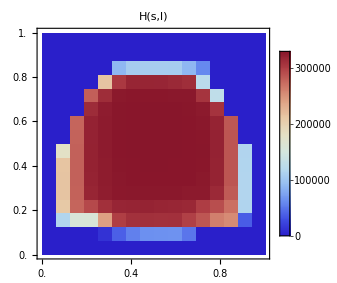

```mathematica
ArrayPlot[Reverse@Transpose@histArrSingle,pltOptMatPlot,ColorFunction->"ThermometerColors",FrameLabel->Reverse[xyLabNoDimLst⟦All,2⟧],DataRange->{{0.5/histDivNum,1-0.5/histDivNum},{0.5/histDivNum,1-0.5/histDivNum}},FrameTicks->{Range[0,1,0.2]},PlotLegends->Automatic,PlotLabel->"H(s,l)",ImageSize->10cm]
```

```mathematica
testArr=ConstantArray[Range[10],10]
```

{{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9,10}}

```mathematica
ListPlot3D[testArr,AxesLabel->{"x","y","h"}]
```

-Graphics3D-

## Wang Landau compute fro g(s,l)

### Z, <s>, <l>

#### 2d

```mathematica
divNum=4;
nDim=3;
grdNum=divNum^nDim;
```

```mathematica
lnkValMax=2grdNum;
```

```mathematica
lnkValLst={-lnkValMax}~Join~Range[-lnkValMax+8,lnkValMax-8,4]~Join~{lnkValMax};
BValLst=Range[-grdNum,grdNum,2];
```

```mathematica
lnkValGrd=ConstantArray[lnkValLst,Length[BValLst]]ᵀ;
BValGrd=ConstantArray[BValLst,Length[lnkValLst]];
```

```mathematica
lnkValGrd//Dimensions
```

{63,65}

```mathematica
ZVal=Total[Exp[dosGlued]dosGluedMask,-1];
```

```mathematica
ZVal
```

8.55373×10^31

```mathematica
dosGlued//Dimensions
```

{63,65}

```mathematica
lnkValLst//Dimensions
```

{63}

```mathematica
cILst=Range[-3,3,0.1];
cMLst=Range[-3,3,0.1];
```

```mathematica
Total[{{1,2},{3,4}},-1]
```

10

```mathematica
cILst
```

{-3.,-2.9,-2.8,-2.7,-2.6,-2.5,-2.4,-2.3,-2.2,-2.1,-2.,-1.9,-1.8,-1.7,-1.6,-1.5,-1.4,-1.3,-1.2,-1.1,-1.,-0.9,-0.8,-0.7,-0.6,-0.5,-0.4,-0.3,-0.2,-0.1,0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.}

```mathematica
cMLst
```

{-3.,-2.9,-2.8,-2.7,-2.6,-2.5,-2.4,-2.3,-2.2,-2.1,-2.,-1.9,-1.8,-1.7,-1.6,-1.5,-1.4,-1.3,-1.2,-1.1,-1.,-0.9,-0.8,-0.7,-0.6,-0.5,-0.4,-0.3,-0.2,-0.1,0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.}

```mathematica
sAvgLst=ConstantArray[0,{Length[cILst],Length[cMLst]}];
```

```mathematica
dosGluedMask=Map[If[#==0,0,1]&,dosGlued,{-1}];
```

```mathematica
sAvgLst=
Table[
Module[{boltzFact,boltzFactG,expBoltzFactG,numer,denom},
boltzFact=-(cI lnkValGrd+cM BValGrd);
boltzFactG=(boltzFact+dosGlued)dosGluedMask;
expBoltzFactG=Exp[boltzFactG]dosGluedMask;
numer=Total[BValGrd expBoltzFactG,-1];
denom=Total[expBoltzFactG,-1];
numer/denom
]
,{cI,cILst},{cM,cMLst}];
```

```mathematica
lAvgLst=
Table[
Module[{boltzFact,boltzFactG,expBoltzFactG,numer,denom},
boltzFact=-(cI lnkValGrd+cM BValGrd);
boltzFactG=(boltzFact+dosGlued)dosGluedMask;
expBoltzFactG=Exp[boltzFactG]dosGluedMask;
numer=Total[lnkValGrd expBoltzFactG,-1];
denom=Total[expBoltzFactG,-1];
numer/denom
]
,{cI,cILst},{cM,cMLst}];
```

```mathematica
cMLst
```

```mathematica
cI=1;cM=0;
```

```mathematica
boltzFact=boltzFact=-(cI lnkValGrd+cM BValGrd);
```

```mathematica
boltzFactG=(boltzFact+dosGlued)dosGluedMask;
```

```mathematica
ListPlot3D[boltzFactG,PlotRange->All]
```

-Graphics3D-

```mathematica
ZVal
```

8.55373×10^31

```mathematica
BValLst
```

{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64}

```mathematica
lnkValLst
```

{0,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,40,42,44,46,48,50,52,54,56,58,60,62,64,66,68,70,72,74,76,78,80,82,84,86,88,90,92,94,96,98,100,102,104,106,108,110,112,114,116,118,120,122,124,128}

```mathematica
sAvgLst⟦All,1⟧
```

{2.21558×10^107,6.13043×10^101,1.69815×10^96,4.71169×10^90,1.31053×10^85,3.65864×10^79,1.02703×10^74,2.90692×10^68,8.33014×10^62,2.43183×10^57,7.30013×10^51,2.28529×10^46,7.61873×10^40,2.78965×10^35,1.17239×10^30,6.01075×10^24,4.09328×10^19,4.23025×10^14,8.51271×10^9,497668.,97.0452,0.0446645,0.0000378308,6.18628×10^-8,2.15325×10^-10,1.37263×10^-12,1.32467×10^-14,1.90969×10^-16,4.8587×10^-18,2.37917×10^-19,1.92669×10^-20,2.28792×10^-21,3.86765×10^-22,8.94175×10^-23,2.60933×10^-23,8.85591×10^-24,3.30072×10^-24,1.30513×10^-24,5.36462×10^-25,2.26421×10^-25,9.73676×10^-26,4.24479×10^-26,1.86999×10^-26,8.30787×10^-27,3.71814×10^-27,1.67563×10^-27,7.60606×10^-28,3.48059×10^-28,1.60816×10^-28,7.51917×10^-29,3.56841×10^-29,1.72523×10^-29,8.53299×10^-30,4.33596×10^-30,2.272×10^-30,1.23066×10^-30,6.89532×10^-31,3.99105×10^-31,2.3792×10^-31,1.45486×10^-31,9.08508×10^-32}

```mathematica
ZVal
```

8.55373×10^31

```mathematica
Min[dosGlued]
```

0.

```mathematica
Max[dosGlued]
```

69.6268

```mathematica
sAvgLst//Dimensions
```

{61,61}

```mathematica
sAvgLst⟦1,1⟧
```

32.0064

```mathematica
1/2.26
```

0.442478

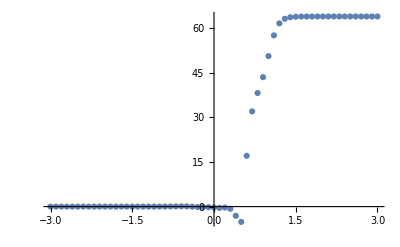

```mathematica
ListPlot[{cILst,sAvgLst⟦All,31⟧}ᵀ]
```

```mathematica
ListPlot3D[sAvgLst/grdNum,PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[lAvgLst/grdNum,PlotRange->All]
```

-Graphics3D-

#### 3d

```mathematica
dosGlued=readJuliaVar[fNameWL,"dosArrGlued"];
```

```mathematica
dosGlued//Dimensions
```

{95,193}

```mathematica
divNum=4;
nDim=3;
grdNum=nDim divNum^nDim;
```

```mathematica
lnkValLst={-grdNum}~Join~Range[-grdNum+8,grdNum-8,4]~Join~{grdNum};
BValLst=Range[-grdNum,grdNum,2];
```

```mathematica
lnkValGrd=Transpose@ConstantArray[lnkValLst,grdNum+1];
BValGrd=ConstantArray[BValLst,grdNum/2-1];
```

```mathematica
Dimensions/@{lnkValGrd,BValGrd}
```

{{95,193},{95,193}}

```mathematica
BValLstᵀ//Dimensions
```

{193}

```mathematica
grdNum
```

```mathematica
Outer[Times,{{3,4}},{1,2}]
```

{{{3,6},{4,8}}}

```mathematica
getBoltzFact[cA_,cL_,sGrd_,lGrd_,grdNum_]:=Exp[-(cA sGrd+cL lGrd)];
```

```mathematica
getLogBoltzFact[cA_,cL_,sGrd_,lGrd_,grdNum_]:=-(cA sGrd+cL lGrd);
```

```mathematica
getZTerms[cA_,cL_,sGrd_,lGrd_,grdNum_]:=dosGlued getBoltzFact[cA,cL,sGrd,lGrd,grdNum];
```

```mathematica
getZTerms[cA_,cL_,sGrd_,lGrd_,grdNum_]:=Exp[dosGlued+ getLogBoltzFact[cA,cL,sGrd,lGrd,grdNum]]Map[If[#==0,0,1]&,dosGlued,{-1}];
```

```mathematica
getZ[cA_,cL_,sGrd_,lGrd_,grdNum_]:=Total[getZTerms[cA,cL,sGrd,lGrd,grdNum],{-1}];
```

```mathematica
getZ[zTerms_]:=Total[zTerms,-1];
```

```mathematica
getAvgS[cA_,cL_,sGrd_,zTerms_,zVal_]:=Total[sGrd zTerms,-1]/zVal;
```

```mathematica
getAvgL[cA_,cL_,lGrd_,zTerms_,zVal_]:=Total[lGrd zTerms,-1]/zVal;
```

```mathematica
Total[{{3,4}},-1]
```

7

```mathematica
Outer[Times,{{1,2},{3,4}},{5,6}]
```

{{{5,6},{10,12}},{{15,18},{20,24}}}

```mathematica
{{1,2},{3,4}}{5,6}
```

{{5,10},{18,24}}

```mathematica
{{1,2},{3,4}}{{5,6}}
```

Thread::tdlen: Objects of unequal length in {{1,2},{3,4}} {{5,6}} cannot be combined.

{{5,6}} {{1,2},{3,4}}

```mathematica
cL=-4;cA=3;
```

```mathematica
zTerms=getZTerms[cA,cL,BValGrd,lnkValGrd,grdNum];
```

```mathematica
zVal=getZ[zTerms];
```

```mathematica
zVal
```

1.03323329036508×10^384281

```mathematica
sA0Ln4=getAvgS[cA,cL,BValGrd,lnkValGrd,zTerms,zVal];
```

```mathematica
lA0Ln4=getAvgL[cA,cL,BValGrd,lnkValGrd,zTerms,zVal];
```

```mathematica
sA0Ln4
```

192.

```mathematica
sA0Ln4/grdNum
```

-0.5

```mathematica
lA0Ln4/grdNum
```

1.

```mathematica
zTerms//Dimensions
```

{95,193}

```mathematica
ListPlot3D[Log[zTerms]]
```

-Graphics3D-

```mathematica
zTerms//Dimensions
```

{95,193}

```mathematica
lVal4=getAvgL[0,-4,BValGrd,lnkValGrd,grdNum]
```

$Aborted

```mathematica
cBnd=2;cIncr=0.1;
cALst=Range[-4cBnd,4cBnd,cIncr];
cLLst=Range[-cBnd,cBnd,cIncr];
```

```mathematica
cALst
```

{-2.,-1.95,-1.9,-1.85,-1.8,-1.75,-1.7,-1.65,-1.6,-1.55,-1.5,-1.45,-1.4,-1.35,-1.3,-1.25,-1.2,-1.15,-1.1,-1.05,-1.,-0.95,-0.9,-0.85,-0.8,-0.75,-0.7,-0.65,-0.6,-0.55,-0.5,-0.45,-0.4,-0.35,-0.3,-0.25,-0.2,-0.15,-0.1,-0.05,0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.,1.05,1.1,1.15,1.2,1.25,1.3,1.35,1.4,1.45,1.5,1.55,1.6,1.65,1.7,1.75,1.8,1.85,1.9,1.95,2.}

```mathematica
cALst={3};
cLLst={-4};
```

```mathematica
slAvgGrd3=Table[
Module[{zTerms,zVal},
zTerms=getZTerms[cA,cL,BValGrd,lnkValGrd,grdNum];
zVal=getZ[zTerms];
{getAvgS[cA,cL,BValGrd,zTerms,zVal],getAvgL[cA,cL,lnkValGrd,zTerms,zVal]}/grdNum
]
,{cA,cALst},{cL,cLLst}];
```

```mathematica
slAvgGrd3
```

{{{-0.499989836482279,0.999999999234899}}}

```mathematica
slAvgGrd//Dimensions
```

{11,11,2}

```mathematica
slAvgGrd301=(slAvgGrd3+1)/2;
```

```mathematica
slAvgGrd01=(slAvgGrd+1)/2;
```

```mathematica
slAvgGrd01⟦All,All,1⟧//MatrixForm
```

(0.75 | 0.75 | 0.75 | 0.75 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.75 | 0.75 | 0.75 | 0.75 | 0.88507312155 | 1. | 1. | 1. | 1. | 1. | 1.
0.75 | 0.75 | 0.75 | 0.75 | 0.75 | 1. | 1. | 1. | 1. | 1. | 1.
0.75 | 0.75 | 0.75 | 0.75 | 0.75 | 1. | 1. | 1. | 1. | 1. | 1.
0.75 | 0.75 | 0.75 | 0.75 | 0.75 | 1. | 1. | 1. | 1. | 1. | 1.
0.4732583759872061 | 0.4732583759872061 | 0.4732583759874993 | 0.4732583759874993 | 0.4732583759874122 | 0.499991 | 0.5936504800001987 | 0.5936504800001987 | 0.5936504800001987 | 0.5936504800001989 | 0.5936504800001989
0.25 | 0.25 | 0.25 | 0.25 | 0.25 | 0. | 0. | 0. | 0. | 0. | 0.
0.25 | 0.25 | 0.25 | 0.25 | 0.25 | 0. | 0. | 0. | 0. | 0. | 0.
0.25 | 0.25 | 0.25 | 0.25 | 0.25 | 0. | 0. | 0. | 0. | 0. | 0.
0.25 | 0.25 | 0.25 | 0.25 | 0.115164884 | 0. | 0. | 0. | 0. | 0. | 0.
0.25 | 0.25 | 0.25 | 0.25 | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

```mathematica
slAvgGrd⟦All,All,1⟧//MatrixForm
```

(0.5 | 0.5 | 0.5 | 0.5 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.5 | 0.5 | 0.5 | 0.5 | 0.77014624309 | 1. | 1. | 1. | 1. | 1. | 1.
0.5 | 0.5 | 0.5 | 0.5 | 0.5 | 1. | 1. | 1. | 1. | 1. | 1.
0.5 | 0.5 | 0.5 | 0.5 | 0.5 | 1. | 1. | 1. | 1. | 1. | 1.
0.5 | 0.5 | 0.5 | 0.5 | 0.5 | 1. | 1. | 1. | 1. | 1. | 1.
-0.0534832480255877 | -0.0534832480255877 | -0.0534832480250013 | -0.0534832480250013 | -0.0534832480251757 | -0.0000176245 | 0.187300960000397 | 0.187300960000397 | 0.187300960000397 | 0.187300960000398 | 0.187300960000398
-0.5 | -0.5 | -0.5 | -0.5 | -0.5 | -1. | -1. | -1. | -1. | -1. | -1.
-0.5 | -0.5 | -0.5 | -0.5 | -0.5 | -1. | -1. | -1. | -1. | -1. | -1.
-0.5 | -0.5 | -0.5 | -0.5 | -0.5 | -1. | -1. | -1. | -1. | -1. | -1.
-0.5 | -0.5 | -0.5 | -0.5 | -0.76967023199 | -1. | -1. | -1. | -1. | -1. | -1.
-0.5 | -0.5 | -0.5 | -0.5 | -1. | -1. | -1. | -1. | -1. | -1. | -1.)

```mathematica
slAvgGrd⟦All,All,2⟧//MatrixForm
```

(1. | 1. | 1. | 1. | -1. | -1. | -1. | -1. | -1. | -1. | -1.
1. | 1. | 1. | 1. | -0.080584972365 | -1. | -1. | -1. | -1. | -1. | -1.
1. | 1. | 1. | 1. | 1. | -1. | -1. | -1. | -1. | -1. | -1.
1. | 1. | 1. | 1. | 1. | -1. | -1. | -1. | -1. | -1. | -1.
1. | 1. | 1. | 1. | 1. | -1. | -1. | -1. | -1. | -1. | -1.
1. | 1. | 1. | 1. | 1. | 0.000205666 | -1. | -1. | -1. | -1. | -1.
1. | 1. | 1. | 1. | 1. | -1. | -1. | -1. | -1. | -1. | -1.
1. | 1. | 1. | 1. | 1. | -1. | -1. | -1. | -1. | -1. | -1.
1. | 1. | 1. | 1. | 1. | -1. | -1. | -1. | -1. | -1. | -1.
1. | 1. | 1. | 1. | -0.078680927977 | -1. | -1. | -1. | -1. | -1. | -1.
1. | 1. | 1. | 1. | -1. | -1. | -1. | -1. | -1. | -1. | -1.)

```mathematica
slAvgGrd
```

{{{-0.5,1.}}}

```mathematica
Table[ii,{ii,{4,5,8,9}}]
```

{4,5,8,9}

```mathematica
testGrd=Table[
{cA,cL}
,{cA,cALst},{cL,cLLst}];
```

```mathematica
testGrd
```

{{{-5,-5},{-5,-4},{-5,-3},{-5,-2},{-5,-1},{-5,0},{-5,1},{-5,2},{-5,3},{-5,4},{-5,5}},{{-4,-5},{-4,-4},{-4,-3},{-4,-2},{-4,-1},{-4,0},{-4,1},{-4,2},{-4,3},{-4,4},{-4,5}},{{-3,-5},{-3,-4},{-3,-3},{-3,-2},{-3,-1},{-3,0},{-3,1},{-3,2},{-3,3},{-3,4},{-3,5}},{{-2,-5},{-2,-4},{-2,-3},{-2,-2},{-2,-1},{-2,0},{-2,1},{-2,2},{-2,3},{-2,4},{-2,5}},{{-1,-5},{-1,-4},{-1,-3},{-1,-2},{-1,-1},{-1,0},{-1,1},{-1,2},{-1,3},{-1,4},{-1,5}},{{0,-5},{0,-4},{0,-3},{0,-2},{0,-1},{0,0},{0,1},{0,2},{0,3},{0,4},{0,5}},{{1,-5},{1,-4},{1,-3},{1,-2},{1,-1},{1,0},{1,1},{1,2},{1,3},{1,4},{1,5}},{{2,-5},{2,-4},{2,-3},{2,-2},{2,-1},{2,0},{2,1},{2,2},{2,3},{2,4},{2,5}},{{3,-5},{3,-4},{3,-3},{3,-2},{3,-1},{3,0},{3,1},{3,2},{3,3},{3,4},{3,5}},{{4,-5},{4,-4},{4,-3},{4,-2},{4,-1},{4,0},{4,1},{4,2},{4,3},{4,4},{4,5}},{{5,-5},{5,-4},{5,-3},{5,-2},{5,-1},{5,0},{5,1},{5,2},{5,3},{5,4},{5,5}}}

```mathematica
slAvgGrd01⟦All,All,1⟧//MatrixForm
```

(0.75 | 0.75 | 0.75 | 0.75 | 0.75 | 0.75 | 0.75 | 0.75 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.75 | 0.75 | 0.75 | 0.75 | 0.75 | 0.75 | 0.75 | 0.75 | 0.999999999999959 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.75 | 0.75 | 0.75 | 0.75 | 0.75 | 0.75 | 0.75 | 0.75 | 0.885073121546 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.75 | 0.75 | 0.75 | 0.75 | 0.75 | 0.75 | 0.75 | 0.75 | 0.75 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.75 | 0.75 | 0.75 | 0.75 | 0.75 | 0.75 | 0.75 | 0.75 | 0.75 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.75 | 0.75 | 0.75 | 0.75 | 0.75 | 0.75 | 0.75 | 0.75 | 0.75 | 0.999999999999959 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.75 | 0.75 | 0.75 | 0.75 | 0.75 | 0.75 | 0.75 | 0.75 | 0.75 | 0.8850731215456 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.75 | 0.75 | 0.75 | 0.75 | 0.75 | 0.75 | 0.75 | 0.75 | 0.75 | 0.75 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.75 | 0.75 | 0.75 | 0.75 | 0.75 | 0.75 | 0.75 | 0.75 | 0.75 | 0.75 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.75 | 0.75 | 0.75 | 0.75 | 0.75 | 0.75 | 0.75 | 0.75 | 0.75 | 0.75 | 0.999999999999959 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.4732583759874122 | 0.4732583759874122 | 0.47325837598739 | 0.47325837598739 | 0.47325837598739 | 0.47325837598739 | 0.4732583759874107 | 0.4732583759874107 | 0.4732583759874003 | 0.4732583759874048 | 0.499991 | 0.5936504800001987 | 0.5936504800001987 | 0.5936504800001987 | 0.5936504800001987 | 0.5936504800001987 | 0.5936504800001987 | 0.5936504800001987 | 0.5936504800001987 | 0.5936504800001987 | 0.5936504800001987
0.25 | 0.25 | 0.25 | 0.25 | 0.25 | 0.25 | 0.25 | 0.25 | 0.25 | 0.25 | 1.02×10^-12 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.25 | 0.25 | 0.25 | 0.25 | 0.25 | 0.25 | 0.25 | 0.25 | 0.25 | 0.25 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.25 | 0.25 | 0.25 | 0.25 | 0.25 | 0.25 | 0.25 | 0.25 | 0.25 | 0.25 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.25 | 0.25 | 0.25 | 0.25 | 0.25 | 0.25 | 0.25 | 0.25 | 0.25 | 0.1151648840029 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.25 | 0.25 | 0.25 | 0.25 | 0.25 | 0.25 | 0.25 | 0.25 | 0.25 | 1.02×10^-12 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.25 | 0.25 | 0.25 | 0.25 | 0.25 | 0.25 | 0.25 | 0.25 | 0.25 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.25 | 0.25 | 0.25 | 0.25 | 0.25 | 0.25 | 0.25 | 0.25 | 0.25 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.25 | 0.25 | 0.25 | 0.25 | 0.25 | 0.25 | 0.25 | 0.25 | 0.115164884003 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.25 | 0.25 | 0.25 | 0.25 | 0.25 | 0.25 | 0.25 | 0.25 | 1.02×10^-12 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.25 | 0.25 | 0.25 | 0.25 | 0.25 | 0.25 | 0.25 | 0.25 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

```mathematica
slAvgGrd01⟦All,All,2⟧//MatrixForm
```

(1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.64×10^-13 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.4597075138177 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.64×10^-13 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.45970751381773 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.64×10^-13 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.500103 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 4.061×10^-12 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.46065953601144 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 4.061×10^-12 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.4606595360115 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 4.061×10^-12 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

```mathematica
slAvgGrd301⟦All,All,2⟧//MatrixForm
```

(1. | 1. | 1. | 1. | 0.999999771951 | 0.459707513817732 | 0.001543067601358 | 3.55368×10^-10 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 1. | 1. | 1. | 0.999999995098 | 0.977819849238 | 0.01685132721355 | 1.6533645×10^-8 | 4.×10^-15 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 1. | 1. | 1. | 0.999999999895 | 0.999511208856 | 0.083450630619553 | 7.69208149×10^-7 | 1.64×10^-13 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 1. | 1. | 1. | 0.999999999998 | 0.99998939214 | 0.293406086920182 | 0.000035728323787 | 7.638×10^-12 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 1. | 1. | 1. | 1. | 0.999999771951 | 0.4597075138177395 | 0.001543067601362 | 3.55368×10^-10 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 1. | 1. | 1. | 1. | 0.999999995098 | 0.977819849238 | 0.016851327213551 | 1.6533645×10^-8 | 4.×10^-15 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 1. | 1. | 1. | 1. | 0.999999999895 | 0.999511208856 | 0.083450630619844 | 7.69208149×10^-7 | 1.64×10^-13 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 1. | 1. | 1. | 1. | 0.999999999998 | 0.99998939214 | 0.293406086910138 | 0.000035728323787 | 7.638×10^-12 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 1. | 1. | 1. | 1. | 1. | 0.999999771951 | 0.4597075138340354 | 0.00154306760136 | 3.55368×10^-10 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 1. | 1. | 1. | 1. | 1. | 0.999999995098 | 0.977819849151 | 0.016851327216202 | 1.6533645×10^-8 | 4.×10^-15 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 1. | 1. | 1. | 1. | 1. | 0.999999999895 | 0.999511208856 | 0.083450631249978 | 7.69208149×10^-7 | 1.64×10^-13 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 1. | 1. | 1. | 1. | 1. | 0.999999999998 | 0.99998939214 | 0.293406065169709 | 0.000035728323787 | 7.638×10^-12 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.999999771951 | 0.4597075490967124 | 0.001543067602059 | 3.55368×10^-10 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.999999995098 | 0.977819660536 | 0.016851332953882 | 1.6533645×10^-8 | 4.×10^-15 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.999999999895 | 0.999511208855 | 0.083451994955591 | 7.6920815×10^-7 | 1.64×10^-13 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.999999999998 | 0.99998939214 | 0.293359221738981 | 0.000035728324485 | 7.638×10^-12 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.999999771951 | 0.4597841698845096 | 0.001543069115498 | 3.55368×10^-10 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.999999995098 | 0.977404015225359 | 0.016864743667985 | 1.6533645×10^-8 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.999999999895 | 0.999511204302877 | 0.084646285288509 | 7.69208847×10^-7 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.999999999997733 | 0.999989380624519 | 0.286565 | 0.000035729845735 | 7.638×10^-12 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.999999999999488 | 0.999998 | 0.500103 | 0.0303663 | 1.7679×10^-11 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.999999999971801 | 0.999866 | 0.286878 | 0.000856212946333 | 1.88952×10^-10 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.999999998819 | 0.995486317666382 | 0.076891979085292 | 0.000019015303557 | 4.×10^-12 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.999999945061 | 0.7801007935009387 | 0.02707592681479 | 4.09000243×10^-7 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.999999999999 | 0.999997444192 | 0.4607326204603632 | 0.013998515507113 | 8.791024×10^-9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.999999999975 | 0.999881671045 | 0.293537416407811 | 0.000849570795284 | 1.88951×10^-10 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.999999998819 | 0.995495465517 | 0.076711296762027 | 0.000019012020143 | 4.061×10^-12 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.999999945061 | 0.7803974408233 | 0.027017001122636 | 4.08998724×10^-7 | 8.7×10^-14 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 1. | 1. | 1. | 1. | 1. | 0.999999999999 | 0.999997444192 | 0.4606595695041731 | 0.013997200780214 | 8.791023×10^-9 | 2.×10^-15 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 1. | 1. | 1. | 1. | 1. | 0.999999999975 | 0.999881671045 | 0.293571478369842 | 0.000849567726634 | 1.88951×10^-10 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 1. | 1. | 1. | 1. | 1. | 0.999999998819 | 0.995495466097 | 0.076711825257172 | 0.000019012018626 | 4.061×10^-12 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 1. | 1. | 1. | 1. | 1. | 0.999999945061 | 0.780397588988 | 0.02701697385358 | 4.08998723×10^-7 | 8.7×10^-14 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 1. | 1. | 1. | 1. | 0.999999999999 | 0.999997444192 | 0.4606595360269324 | 0.013997200172802 | 8.791023×10^-9 | 2.×10^-15 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 1. | 1. | 1. | 1. | 0.999999999975 | 0.999881671045 | 0.293571494160516 | 0.000849567725217 | 1.88951×10^-10 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 1. | 1. | 1. | 1. | 0.999999998819 | 0.995495466098 | 0.076711825501564 | 0.000019012018625 | 4.061×10^-12 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 1. | 1. | 1. | 1. | 0.999999945061 | 0.780397589056 | 0.027016973840981 | 4.08998723×10^-7 | 8.7×10^-14 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 1. | 1. | 1. | 0.999999999999 | 0.999997444192 | 0.4606595360114669 | 0.013997200172521 | 8.791023×10^-9 | 2.×10^-15 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 1. | 1. | 1. | 0.999999999975 | 0.999881671045 | 0.293571494167813 | 0.000849567725214 | 1.88951×10^-10 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 1. | 1. | 1. | 0.999999998819 | 0.995495466098 | 0.076711825501681 | 0.000019012018625 | 4.061×10^-12 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 1. | 1. | 1. | 0.999999945061 | 0.780397589056 | 0.027016973840975 | 4.08998723×10^-7 | 8.7×10^-14 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1. | 1. | 1. | 0.999999999999 | 0.999997444192 | 0.4606595360114573 | 0.013997200172513 | 8.791023×10^-9 | 2.×10^-15 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

```mathematica
ListPlot3D[slAvgGrd301⟦All,All,2⟧,ColorFunction->"ThermometerColors"]
```

-Graphics3D-

```mathematica
ListPlot3D[slAvgGrd301⟦All,All,1⟧,ColorFunction->"ThermometerColors"]
```

-Graphics3D-

```mathematica
cALst
```

{-0.2,-0.19,-0.18,-0.17,-0.16,-0.15,-0.14,-0.13,-0.12,-0.11,-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2}

```mathematica
cLLst
```

{-0.1,-0.09,-0.08,-0.07,-0.06,-0.05,-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}

```mathematica
sData=Flatten[Table[{cALst⟦iA⟧,cLLst⟦iL⟧,slAvgGrd301⟦iA,iL,1⟧},{iA,Length[cALst]},{iL,Length[cLLst]}],1];
lData=Flatten[Table[{cALst⟦iA⟧,cLLst⟦iL⟧,slAvgGrd301⟦iA,iL,2⟧},{iA,Length[cALst]},{iL,Length[cLLst]}],1];
```

```mathematica
sData//Dimensions
```

{861,3}

```mathematica
ListPlot3D[sData,ColorFunction->"ThermometerColors"]
```

-Graphics3D-

```mathematica
ListPlot3D[sData,ColorFunction->"ThermometerColors"]
```

-Graphics3D-

```mathematica
ListPlot3D[sData,ColorFunction->"ThermometerColors"]
```

-Graphics3D-

```mathematica
ListPlot3D[sData,ColorFunction->"ThermometerColors"]
```

-Graphics3D-

```mathematica
ListPlot3D[lData,ColorFunction->"ThermometerColors"]
```

-Graphics3D-

```mathematica
ListPlot3D[lData,ColorFunction->"ThermometerColors"]
```

-Graphics3D-

```mathematica
ListPlot3D[lData,ColorFunction->"ThermometerColors"]
```

-Graphics3D-

```mathematica
cAcLLab=matexLstFunc[{"c_A","c_L"},labMag];
```

```mathematica
sl01Lab=matexLstFunc[{"\\langle s + 1 \\rangle /2","\\langle l + 1 \\rangle /2"},labMag];
```

```mathematica
cAcLLab
```

{-Graphics-,-Graphics-}

```mathematica
sl01Lab
```

{-Graphics-,-Graphics-}

```mathematica
sl01Lab⟦1;;1⟧
```

{-Graphics-}

```mathematica
pltSVscAcL=ListPlot3D[sData,ColorFunction->"ThermometerColors",BaseStyle->texStyle,AxesLabel->cAcLLab~Join~sl01Lab⟦1;;1⟧]
```

-Graphics3D-

```mathematica
pltLVscAcL=ListPlot3D[lData,ColorFunction->"ThermometerColors",BaseStyle->texStyle,AxesLabel->cAcLLab~Join~sl01Lab⟦2;;2⟧]
```

-Graphics3D-

```mathematica
Export[dirFigsDoc<>"sVs_cAcL.pdf",pltSVscAcL];
Export[dirFigsDoc<>"lVs_cAcL.pdf",pltLVscAcL2];
```

Export::noopen: Cannot open ./figs/figsDoc/sVs_cAcL.pdf.

```mathematica
dirFigsDoc
```

./figs/figsDoc/

```mathematica
pltLVscAcL2=%296
```

-Graphics3D-

```mathematica
pltLVscAcL2=-Graphics3D-
```

-Graphics3D-

```mathematica
pltGslDiv4=-Graphics3D-
```

-Graphics3D-

```mathematica
lnkValLst//Dimensions
```

{95}

```mathematica
dosGlued//Dimensions
```

{95,193}

```mathematica
dosGluedCoords=Flatten[Table[{(BValLst⟦iB⟧/grdNum+1)/2,(lnkValLst⟦iL⟧/grdNum+1)/2,If[#==0||#<dosGlued⟦1,1⟧,0,#-dosGlued⟦1,1⟧]&@dosGlued⟦iL,iB⟧},{iB,Length[BValLst]},{iL,Length[lnkValLst]}],1];
```

```mathematica
labLogG=matexLstFunc[{"\\log g \\left( s, \\ell \\right)"},labMag];
```

```mathematica
pltGslDiv4=ListPlot3D[dosGluedCoords,PlotRange->All,ColorFunction->"ThermometerColors",AxesLabel->sl01Lab~Join~labLogG,PlotLegends->Automatic,BaseStyle->texStyle]
```

-Graphics3D-

```mathematica
pltGslDiv4Rot=-Graphics3D-
```

-Graphics3D-

```mathematica
ListPlot3D[Map[If[#==0||#<dosGlued⟦1,1⟧,0,#-dosGlued⟦1,1⟧]&,dosGlued,{-1}],PlotRange->All,ColorFunction->"ThermometerColors",AxesLabel->{"s_total","l_total","log g(s,l)"},PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
Export[dirFigsDoc<>"g_slDiv4.pdf",pltGslDiv4Rot];
```

```mathematica
pltGslDiv4//Options
```

{}

```mathematica
pltGslDiv4Rot⟦1⟧//Options
```

{Axes→True,AxesLabel→{-Graphics-,-Graphics-,log g(s,l)},BaseStyle→{FontFamily→Times New Roman,FontSize→8,FontWeight→Plain},BoxRatios→{1,1,0.4},DisplayFunction→Identity,FaceGridsStyle→Automatic,ImageSize→{360.,322.072},Lighting→Neutral,Method→{DefaultBoundaryStyle→Directive[GrayLevel[0.3]],DefaultGraphicsInteraction→{Version→1.2,TrackMousePosition→{True,False},Effects→{Highlight→{ratio→2},HighlightPoint→{ratio→2},Droplines→{freeformCursorMode→True,placement→{x→All,y→None}}}},RotationControl→Globe},PlotRange→{All,All,All},PlotRangePadding→{{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Scaled[0.02]}},SphericalRegion→True,Ticks→{Automatic,Automatic,Automatic},ViewAngle→0.437823,ViewPoint→{0.87791,-1.55847,2.87236},ViewVertical→{-0.41662,0.739588,0.528619}}

```mathematica
Options[-Graphics3D-]
```

{}

```mathematica
ListPlot3D[dosGluedCoords,PlotRange->All,ColorFunction->"ThermometerColors",AxesLabel->sl01Lab~Join~labLogG,BaseStyle->texStyle,ViewAngle->0.43782284161739216,ViewPoint->{0.8779099027838034,-1.5584722479745492,2.872357647453967},ViewVertical->{-0.41662035514881135,0.7395875811194937,0.5286186617302634},PlotRangePadding->Automatic,ImageSize->{15cm,11cm}]
```

-Graphics3D-

```mathematica
pltGslDiv4Rot=ListPlot3D[dosGluedCoords,PlotRange->All,ColorFunction->"ThermometerColors",AxesLabel->sl01Lab~Join~labLogG,PlotLegends->Automatic,BaseStyle->texStyle,ViewAngle->0.43782284161739216,ViewPoint->{0.8779099027838034,-1.5584722479745492,2.872357647453967},ViewVertical->{-0.41662035514881135,0.7395875811194937,0.5286186617302634},PlotRangePadding->Automatic,ImagePadding->0.5cm,ImageSize->{15cm,11cm}]
```

-Graphics3D-